# Lab 2: James Fariello, Chris Greene, Michael Imbimbo

## Abstract:

We set out ot understand more how oscilating motion works with friction as it’s secondary force, unlike the first lab where air resistance was the secondary force (gravity was the primary force in both labs). I say primary and secondary because the magnitude of gravity is far larger for both situations, however friction and drag both work with gravity in the beginnng of these motions and against in the end.  Both us taking a cart and sliding it up a ramp at a set angel and watching it come down, and throwing a ball in the air are demonstrative of oscilating motion; they just only go for one osscilation.  
Our goal in this lab was to find an addequate force analysis and match it to our recorded motion. We looked at three different angles (3.7deg, 7.9deg, & 12.9deg) and using the loggerpro system we measured a cart’s position, speed, & acceleration as it went up the track and came back down.  Using this data we plotted the carts position over time and then set out to find a force model to match.  Using the free body diagram below, we mapped the active forces as friction and gravity, the normal force is present and it serves as a significant component of friction.

In the model’s below we set out to find the best model for the friction force and the best coeficient of friction (μ0) to fit all 3 of our models. We used three ways to look at the friction force: purely based on sliding friction (a v^0 componant, Ff=μ0 Fn (-vx/(| vx |)) ), a static drag inspired model (a v^1componant Ff=μ0 Fn (-vx/(| vx |)) vx ), and a dynamic drag inspired model (a v^2componant Ff=μ0 Fn (-vx/(| vx |)) (vx^2) ).  Using the manipulate command, we found appropripate values for μ0 for each model to give the best fit. Our goal for best fit was to match up the starting points and the ending points.

## Model for Angle of 3.7 (friction model)

{{0.966657,0.252791},{0.99999,0.288292},{1.03332,0.320705},{1.06666,0.352776},{1.09999,0.383989},{1.13332,0.417603},{1.16666,0.447615},{1.19999,0.473169},{1.23332,0.501809},{1.26665,0.529249},{1.29999,0.556346},{1.33332,0.582243},{1.36665,0.607968},{1.39999,0.632492},{1.43332,0.656674},{1.46665,0.679826},{1.49999,0.702464},{1.53332,0.724245},{1.56665,0.745511},{1.59998,0.765748},{1.63332,0.785642},{1.66665,0.804335},{1.69998,0.822857},{1.73332,0.840179},{1.76665,0.857157},{1.79998,0.872935},{1.83332,0.888199},{1.86665,0.902433},{1.89998,0.916325},{1.93331,0.929187},{1.96665,0.941535},{1.99998,0.952854},{2.03331,0.963487},{2.06665,0.973777},{2.09998,0.982867},{2.13331,0.991613},{2.16665,0.999331},{2.19998,1.00653},{2.23331,1.01288},{2.26664,1.01871},{2.29998,1.02351},{2.33331,1.02797},{2.36664,1.0314},{2.39998,1.03432},{2.43331,1.0362},{2.46664,1.03775},{2.49998,1.03826},{2.53331,1.03826},{2.56664,1.0374},{2.59997,1.03603},{2.63331,1.0338},{2.66664,1.0314},{2.69997,1.0278},{2.73331,1.02368},{2.76664,1.0194},{2.79997,1.01408},{2.83331,1.00842},{2.86664,1.00156},{2.89997,0.994529},{2.9333,0.98664},{2.96664,0.978579},{2.99997,0.969318},{3.0333,0.959886},{3.06664,0.949424},{3.09997,0.938791},{3.1333,0.927129},{3.16664,0.915124},{3.19997,0.902262},{3.2333,0.889056},{3.26663,0.874993},{3.29997,0.860416},{3.3333,0.844981},{3.36663,0.829374},{3.39997,0.812739},{3.4333,0.795417},{3.46663,0.777924},{3.49997,0.759402},{3.5333,0.740537},{3.56663,0.720815},{3.59996,0.700749},{3.6333,0.679826},{3.66663,0.65856},{3.69996,0.636265},{3.7333,0.613799},{3.76663,0.590303},{3.79996,0.566636},{3.8333,0.541769},{3.86663,0.516901},{3.89996,0.490833},{3.93329,0.464765},{3.96663,0.438354}}

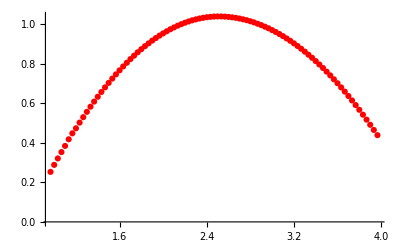

```mathematica
angle37Data={{"Latest: Time (s)","Latest: Position (m)","Latest: Velocity (m/s)","Latest: Acceleration (m/sÂ.b2)"},{0.033333,0.1836765,-0.00743174098408,0.0923736530194},{0.066666,0.1833335,-0.00414462477958,0.0800230240636},{0.099999,0.1833335,-0.00120051200512,0.0558815342918},{0.133332,0.1833335,-0.000285836191695,0.0294890620005},{0.166665,0.1833335,0.000142918095848,0.0182460593638},{0.199998,0.1833335,0.00057167238339,0.0156496879922},{0.233331,0.1833335,0.00171501715017,0.000595498021012},{0.266664,0.183505,0.00128626286263,-0.028822104217},{0.299997,0.183505,-0.00128626286263,-0.0287030046128},{0.33333,0.1833335,-0.00171501715017,0.000238199208405},{0.366663,0.1833335,-0.00057167238339,0.0125054584413},{0.399996,0.1833335,0,-0.0048830837723},{0.433329,0.1833335,-0.000571672383391,-0.0270356101539},{0.466662,0.1833335,-0.00128626286263,-0.0510937302028},{0.499995,0.183505,-0.00843216765501,0.0425185587003},{0.533328,0.182133,0.00100042667093,0.160784465673},{0.566661,0.183848,0.00585964192975,0.166977645092},{0.599994,0.182476,0.0111476114761,0.144706019106},{0.633327,0.1840195,0.0264398477318,-0.157449676756},{0.66666,0.1857345,0.00314419810865,-0.478542209685},{0.699993,0.184534,-0.0264398477318,-0.247965375949},{0.733326,0.182476,-0.0190081067477,0.172456226885},{0.766659,0.1829905,-0.00200085334187,0.397435379223},{0.799992,0.183162,-0.00171501715017,1.14657188966},{0.833325,0.182819,0.0280119467861,3.33264512479},{0.866658,0.1823045,0.16106869402,6.90265576076},{0.899991,0.184534,0.539087057537,8.75548830333},{0.933324,0.219177,0.891808918089,6.37540181295},{0.966657,0.252791,1.00085542522,2.64401121329},{0.99999,0.2882915,1.00957342907,0.340863067227},{1.033323,0.320705,0.976988103214,-0.446980814572},{1.066656,0.3527755,0.960266686,-0.465679452431},{1.099989,0.3839885,0.957551242179,-0.680535138412},{1.133322,0.4176025,0.929110541105,-1.19433083094},{1.166655,0.447615,0.858366083661,-1.18980504598},{1.199988,0.4731685,0.829210792108,-0.634800890399},{1.233321,0.501809,0.829639546395,-0.389813004554},{1.266654,0.529249,0.815347736811,-0.479971404936},{1.299987,0.556346,0.795625039584,-0.580610570487},{1.33332,0.5822425,0.774330243302,-0.629203209001},{1.366653,0.6079675,0.753178365117,-0.646472651611},{1.399986,0.632492,0.731026060261,-0.651951233404},{1.433319,0.6566735,0.709588345883,-0.6518321338},{1.466652,0.679826,0.687436041027,-0.648020946465},{1.499985,0.702464,0.666284162842,-0.641708667443},{1.533318,0.7242445,0.645132284656,-0.648020946465},{1.566651,0.7455105,0.6229799798,-0.6518321338},{1.599984,0.7657475,0.601542265423,-0.651951233404},{1.633317,0.7856415,0.579389960566,-0.648973743299},{1.66665,0.804335,0.558238082381,-0.646829950423},{1.699983,0.822857,0.5369432861,-0.664337592241},{1.733316,0.8401785,0.51421930886,-0.689348509123},{1.766649,0.857157,0.490780741141,-0.706737051337},{1.799982,0.872935,0.466341746751,-0.70030567271},{1.833315,0.8881985,0.443331933319,-0.672436365327},{1.866648,0.902433,0.421894218942,-0.654928723509},{1.899981,0.9163245,0.400599422661,-0.663622994616},{1.933314,0.929187,0.377875445421,-0.678034046724},{1.966647,0.941535,0.35486563199,-0.677676747912},{1.99998,0.952854,0.331569982366,-0.648497344882},{2.033313,0.963487,0.312276039427,-0.635039089607},{2.066646,0.973777,0.290409570762,-0.652546731425},{2.099979,0.9828665,0.26811434781,-0.655762420738},{2.133312,0.991613,0.246533715337,-0.654452325092},{2.166645,0.9993305,0.224381410481,-0.648497344882},{2.199978,1.0065335,0.203229532295,-0.641113169421},{2.233311,1.012879,0.18207765411,-0.644805257152},{2.266644,1.01871,0.160068267349,-0.645400755173},{2.299977,1.023512,0.138916389164,-0.644328858735},{2.33331,1.027971,0.117621592883,-0.655166922717},{2.366643,1.031401,0.0951834518345,-0.663384795407},{2.399976,1.0343165,0.0727453107864,-0.655166922717},{2.433309,1.036203,0.0514505145051,-0.644209759131},{2.466642,1.0377465,0.0302986363197,-0.644328858735},{2.499975,1.038261,0.00828924955916,-0.638850276942},{2.533308,1.038261,-0.0127197105304,-0.620747137103},{2.566641,1.0374035,-0.0331569982366,-0.600142905576},{2.599974,1.0360315,-0.0528796954636,-0.578824076424},{2.633307,1.033802,-0.0708873755404,-0.578347678007},{2.66664,1.031401,-0.0908959089591,-0.58978124001},{2.699973,1.0277995,-0.11219070524,-0.554289557958},{2.733306,1.0236835,-0.127482941496,-0.531541533555},{2.766639,1.019396,-0.145347703477,-0.567509614024},{2.799972,1.0140795,-0.165356236896,-0.603239495285},{2.833305,1.00842,-0.186936869369,-0.601333901618},{2.866638,1.00156,-0.206802484692,-0.560363637772},{2.899971,0.9945285,-0.223809738097,-0.531898832368},{2.933304,0.9866395,-0.240674073407,-0.546190784872},{2.966637,0.978579,-0.259968016347,-0.570248904921},{2.99997,0.969318,-0.279690713574,-0.5696534069},{3.033303,0.9598855,-0.298270066034,-0.558934442522},{3.066636,0.949424,-0.316563582302,-0.556433350834},{3.099969,0.938791,-0.335000016667,-0.563460227482},{3.133302,0.927129,-0.354436877702,-0.563460227482},{3.166635,0.915124,-0.372873312066,-0.556433350834},{3.199968,0.9022615,-0.391166828335,-0.559053542126},{3.233301,0.889056,-0.409746180795,-0.570725303338},{3.266634,0.874993,-0.429468878022,-0.57560838711},{3.299967,0.8604155,-0.448905739057,-0.562388331044},{3.3333,0.8449805,-0.466484664847,-0.559291741334},{3.366633,0.829374,-0.485206935403,-0.578585877215},{3.399966,0.8127385,-0.506501731684,-0.563341127877},{3.433299,0.795417,-0.523080230802,-0.54047400387},{3.466632,0.777924,-0.541087910879,-0.552145765082},{3.499965,0.759402,-0.560238935723,-0.556671550042},{3.533298,0.740537,-0.578675370087,-0.551073868644},{3.566631,0.7208145,-0.59682596826,-0.548334577748},{3.599964,0.700749,-0.614976566432,-0.552383964291},{3.633297,0.679826,-0.633413000797,-0.562626530252},{3.66663,0.65856,-0.652849861832,-0.563222028273},{3.699963,0.636265,-0.671286296196,-0.555718753208},{3.733296,0.6137985,-0.689579812465,-0.555718753208},{3.766629,0.590303,-0.708016246829,-0.562626530252},{3.799962,0.566636,-0.727453107864,-0.559291741334},{3.833295,0.5417685,-0.745889542229,-0.537377414161},{3.866628,0.516901,-0.763325549922,-0.520822569177},{3.899961,0.490833,-0.780332803328,-0.518678776301},{3.933294,0.464765,-0.794624612913,-0.59656991745},{3.966627,0.438354,-0.821493214932,-0.637540181295},{3.99996,0.4097135,-0.841358830255,-0.56739051442},{4.033293,0.382102,-0.857222738894,-0.538449310599},{4.066626,0.3527755,-0.877088354217,-0.50105203488},{4.099959,0.323449,-0.892237672377,-0.375759251259},{4.133292,0.293265,-0.906958236249,0.0656238819155},{4.166625,0.263081,-0.910817024837,1.39286987115},{4.199958,0.2316965,-0.862653626536,4.06903797757},{4.233291,0.200312,-0.654564878982,6.89741537817},{4.266624,0.1833335,-0.317421090878,7.14037857075},{4.299957,0.1829905,-0.0843216765501,4.57294840296},{4.33329,0.1833335,-0.0167214172142,1.85438083743},{4.366623,0.183162,-0.0124338743387,0.535471820494},{4.399956,0.1819615,-0.00786049527162,0.212116395084},{4.433289,0.182819,-0.00500213335467,0.256064149035},{4.466622,0.1812755,0.00743174098408,0.366350382527},{4.499955,0.182819,0.0308703087031,0.169597836384},{4.533288,0.184534,0.0230098134315,-0.153876688629},{4.566621,0.1843625,0.0117192838595,-0.247608077137},{4.599954,0.1850485,0.00528796954636,-0.258327041515},{4.633287,0.18522,-0.0108617752844,-0.103021157635},{4.66662,0.183505,-0.00500213335467,0.118623205786},{4.699953,0.184534,0.00814633146331,0.0634800890399},{4.733286,0.184877,0.0027154438211,-0.0697923680626},{4.766619,0.1850485,-0.0092896762301,0.0749136510433},{4.799952,0.1829905,0.00728882288823,0.197943542184},{4.833285,0.1853915,0.0254394210609,-0.200063515139},{4.866618,0.1867635,-0.00814633146331,-0.525276894374},{4.899951,0.184534,-0.0343003430034,-0.210949218963},{4.933284,0.1829905,-0.0234099840998,0.169216717651},{4.966617,0.1829905,-0.00986134861349,0.269010276012},{4.99995,0.1829905,-0.00257252572526,0.26640199468}};
Data1 = Table[{angle37Data[[n,1]],angle37Data[[n,2]]},{n,30,120}]
Experiment1= ListPlot[Data1,PlotStyle->Red]
```

```mathematica
(* define constants and initial conditions *)
(*{0.933324,0.219177,0.891808918089,6.37540181295}, 1 before start
{0.99999,0.2882915,1.00957342907,0.340863067227},1 after start
{1.033323,0.320705,0.976988103214,-0.446980814572}, 2 after start*)
Manipulate[g = 9.81;
x=0.2882915;
vx=1.00957342907;
ti =0.99999;
tf = 3.966627;
dt = .02;
m=0.467;
theta=3.7Degree;
(*μ0 = 0.0404;*)
(* define an array where we store the results of the simulation *) 
modeldata ={{ti,x}};


(* set up the procedure for step-by-step solution of the equation of motion *)
For[t=ti,t<=tf,
(* calculate the acceleration *)
gx=-m g Sin[theta];
normal=m g Cos[theta];
fx=μ0 normal ((- vx)/Abs[vx]);
ax = (gx+fx)/m;

(* redefine y, vy, in terms of the values from the previous step *)
vx = vx + ax dt;
x = x + vx dt ;
t= t + dt;

(* add the results of the calculation step to the array *)
modeldata = Append[modeldata,{t,x}];

];
(* plot the simulation and compare with the exact result *)
dataplot = ListPlot[modeldata];
Show[{dataplot,Experiment1}],{μ0,0,0.1}]
```

μ0 = 0.0016

## Model for Angle of 3.7 (Static model)

```mathematica
angle37Data={{"Latest: Time (s)","Latest: Position (m)","Latest: Velocity (m/s)","Latest: Acceleration (m/sÂ.b2)"},{0.033333,0.1836765,-0.00743174098408,0.0923736530194},{0.066666,0.1833335,-0.00414462477958,0.0800230240636},{0.099999,0.1833335,-0.00120051200512,0.0558815342918},{0.133332,0.1833335,-0.000285836191695,0.0294890620005},{0.166665,0.1833335,0.000142918095848,0.0182460593638},{0.199998,0.1833335,0.00057167238339,0.0156496879922},{0.233331,0.1833335,0.00171501715017,0.000595498021012},{0.266664,0.183505,0.00128626286263,-0.028822104217},{0.299997,0.183505,-0.00128626286263,-0.0287030046128},{0.33333,0.1833335,-0.00171501715017,0.000238199208405},{0.366663,0.1833335,-0.00057167238339,0.0125054584413},{0.399996,0.1833335,0,-0.0048830837723},{0.433329,0.1833335,-0.000571672383391,-0.0270356101539},{0.466662,0.1833335,-0.00128626286263,-0.0510937302028},{0.499995,0.183505,-0.00843216765501,0.0425185587003},{0.533328,0.182133,0.00100042667093,0.160784465673},{0.566661,0.183848,0.00585964192975,0.166977645092},{0.599994,0.182476,0.0111476114761,0.144706019106},{0.633327,0.1840195,0.0264398477318,-0.157449676756},{0.66666,0.1857345,0.00314419810865,-0.478542209685},{0.699993,0.184534,-0.0264398477318,-0.247965375949},{0.733326,0.182476,-0.0190081067477,0.172456226885},{0.766659,0.1829905,-0.00200085334187,0.397435379223},{0.799992,0.183162,-0.00171501715017,1.14657188966},{0.833325,0.182819,0.0280119467861,3.33264512479},{0.866658,0.1823045,0.16106869402,6.90265576076},{0.899991,0.184534,0.539087057537,8.75548830333},{0.933324,0.219177,0.891808918089,6.37540181295},{0.966657,0.252791,1.00085542522,2.64401121329},{0.99999,0.2882915,1.00957342907,0.340863067227},{1.033323,0.320705,0.976988103214,-0.446980814572},{1.066656,0.3527755,0.960266686,-0.465679452431},{1.099989,0.3839885,0.957551242179,-0.680535138412},{1.133322,0.4176025,0.929110541105,-1.19433083094},{1.166655,0.447615,0.858366083661,-1.18980504598},{1.199988,0.4731685,0.829210792108,-0.634800890399},{1.233321,0.501809,0.829639546395,-0.389813004554},{1.266654,0.529249,0.815347736811,-0.479971404936},{1.299987,0.556346,0.795625039584,-0.580610570487},{1.33332,0.5822425,0.774330243302,-0.629203209001},{1.366653,0.6079675,0.753178365117,-0.646472651611},{1.399986,0.632492,0.731026060261,-0.651951233404},{1.433319,0.6566735,0.709588345883,-0.6518321338},{1.466652,0.679826,0.687436041027,-0.648020946465},{1.499985,0.702464,0.666284162842,-0.641708667443},{1.533318,0.7242445,0.645132284656,-0.648020946465},{1.566651,0.7455105,0.6229799798,-0.6518321338},{1.599984,0.7657475,0.601542265423,-0.651951233404},{1.633317,0.7856415,0.579389960566,-0.648973743299},{1.66665,0.804335,0.558238082381,-0.646829950423},{1.699983,0.822857,0.5369432861,-0.664337592241},{1.733316,0.8401785,0.51421930886,-0.689348509123},{1.766649,0.857157,0.490780741141,-0.706737051337},{1.799982,0.872935,0.466341746751,-0.70030567271},{1.833315,0.8881985,0.443331933319,-0.672436365327},{1.866648,0.902433,0.421894218942,-0.654928723509},{1.899981,0.9163245,0.400599422661,-0.663622994616},{1.933314,0.929187,0.377875445421,-0.678034046724},{1.966647,0.941535,0.35486563199,-0.677676747912},{1.99998,0.952854,0.331569982366,-0.648497344882},{2.033313,0.963487,0.312276039427,-0.635039089607},{2.066646,0.973777,0.290409570762,-0.652546731425},{2.099979,0.9828665,0.26811434781,-0.655762420738},{2.133312,0.991613,0.246533715337,-0.654452325092},{2.166645,0.9993305,0.224381410481,-0.648497344882},{2.199978,1.0065335,0.203229532295,-0.641113169421},{2.233311,1.012879,0.18207765411,-0.644805257152},{2.266644,1.01871,0.160068267349,-0.645400755173},{2.299977,1.023512,0.138916389164,-0.644328858735},{2.33331,1.027971,0.117621592883,-0.655166922717},{2.366643,1.031401,0.0951834518345,-0.663384795407},{2.399976,1.0343165,0.0727453107864,-0.655166922717},{2.433309,1.036203,0.0514505145051,-0.644209759131},{2.466642,1.0377465,0.0302986363197,-0.644328858735},{2.499975,1.038261,0.00828924955916,-0.638850276942},{2.533308,1.038261,-0.0127197105304,-0.620747137103},{2.566641,1.0374035,-0.0331569982366,-0.600142905576},{2.599974,1.0360315,-0.0528796954636,-0.578824076424},{2.633307,1.033802,-0.0708873755404,-0.578347678007},{2.66664,1.031401,-0.0908959089591,-0.58978124001},{2.699973,1.0277995,-0.11219070524,-0.554289557958},{2.733306,1.0236835,-0.127482941496,-0.531541533555},{2.766639,1.019396,-0.145347703477,-0.567509614024},{2.799972,1.0140795,-0.165356236896,-0.603239495285},{2.833305,1.00842,-0.186936869369,-0.601333901618},{2.866638,1.00156,-0.206802484692,-0.560363637772},{2.899971,0.9945285,-0.223809738097,-0.531898832368},{2.933304,0.9866395,-0.240674073407,-0.546190784872},{2.966637,0.978579,-0.259968016347,-0.570248904921},{2.99997,0.969318,-0.279690713574,-0.5696534069},{3.033303,0.9598855,-0.298270066034,-0.558934442522},{3.066636,0.949424,-0.316563582302,-0.556433350834},{3.099969,0.938791,-0.335000016667,-0.563460227482},{3.133302,0.927129,-0.354436877702,-0.563460227482},{3.166635,0.915124,-0.372873312066,-0.556433350834},{3.199968,0.9022615,-0.391166828335,-0.559053542126},{3.233301,0.889056,-0.409746180795,-0.570725303338},{3.266634,0.874993,-0.429468878022,-0.57560838711},{3.299967,0.8604155,-0.448905739057,-0.562388331044},{3.3333,0.8449805,-0.466484664847,-0.559291741334},{3.366633,0.829374,-0.485206935403,-0.578585877215},{3.399966,0.8127385,-0.506501731684,-0.563341127877},{3.433299,0.795417,-0.523080230802,-0.54047400387},{3.466632,0.777924,-0.541087910879,-0.552145765082},{3.499965,0.759402,-0.560238935723,-0.556671550042},{3.533298,0.740537,-0.578675370087,-0.551073868644},{3.566631,0.7208145,-0.59682596826,-0.548334577748},{3.599964,0.700749,-0.614976566432,-0.552383964291},{3.633297,0.679826,-0.633413000797,-0.562626530252},{3.66663,0.65856,-0.652849861832,-0.563222028273},{3.699963,0.636265,-0.671286296196,-0.555718753208},{3.733296,0.6137985,-0.689579812465,-0.555718753208},{3.766629,0.590303,-0.708016246829,-0.562626530252},{3.799962,0.566636,-0.727453107864,-0.559291741334},{3.833295,0.5417685,-0.745889542229,-0.537377414161},{3.866628,0.516901,-0.763325549922,-0.520822569177},{3.899961,0.490833,-0.780332803328,-0.518678776301},{3.933294,0.464765,-0.794624612913,-0.59656991745},{3.966627,0.438354,-0.821493214932,-0.637540181295},{3.99996,0.4097135,-0.841358830255,-0.56739051442},{4.033293,0.382102,-0.857222738894,-0.538449310599},{4.066626,0.3527755,-0.877088354217,-0.50105203488},{4.099959,0.323449,-0.892237672377,-0.375759251259},{4.133292,0.293265,-0.906958236249,0.0656238819155},{4.166625,0.263081,-0.910817024837,1.39286987115},{4.199958,0.2316965,-0.862653626536,4.06903797757},{4.233291,0.200312,-0.654564878982,6.89741537817},{4.266624,0.1833335,-0.317421090878,7.14037857075},{4.299957,0.1829905,-0.0843216765501,4.57294840296},{4.33329,0.1833335,-0.0167214172142,1.85438083743},{4.366623,0.183162,-0.0124338743387,0.535471820494},{4.399956,0.1819615,-0.00786049527162,0.212116395084},{4.433289,0.182819,-0.00500213335467,0.256064149035},{4.466622,0.1812755,0.00743174098408,0.366350382527},{4.499955,0.182819,0.0308703087031,0.169597836384},{4.533288,0.184534,0.0230098134315,-0.153876688629},{4.566621,0.1843625,0.0117192838595,-0.247608077137},{4.599954,0.1850485,0.00528796954636,-0.258327041515},{4.633287,0.18522,-0.0108617752844,-0.103021157635},{4.66662,0.183505,-0.00500213335467,0.118623205786},{4.699953,0.184534,0.00814633146331,0.0634800890399},{4.733286,0.184877,0.0027154438211,-0.0697923680626},{4.766619,0.1850485,-0.0092896762301,0.0749136510433},{4.799952,0.1829905,0.00728882288823,0.197943542184},{4.833285,0.1853915,0.0254394210609,-0.200063515139},{4.866618,0.1867635,-0.00814633146331,-0.525276894374},{4.899951,0.184534,-0.0343003430034,-0.210949218963},{4.933284,0.1829905,-0.0234099840998,0.169216717651},{4.966617,0.1829905,-0.00986134861349,0.269010276012},{4.99995,0.1829905,-0.00257252572526,0.26640199468}};
Data1 = Table[{angle37Data[[n,1]],angle37Data[[n,2]]},{n,30,120}]
Experiment1= ListPlot[Data1,PlotStyle->Red]
```

{{0.966657,0.252791},{0.99999,0.288292},{1.03332,0.320705},{1.06666,0.352776},{1.09999,0.383989},{1.13332,0.417603},{1.16666,0.447615},{1.19999,0.473169},{1.23332,0.501809},{1.26665,0.529249},{1.29999,0.556346},{1.33332,0.582243},{1.36665,0.607968},{1.39999,0.632492},{1.43332,0.656674},{1.46665,0.679826},{1.49999,0.702464},{1.53332,0.724245},{1.56665,0.745511},{1.59998,0.765748},{1.63332,0.785642},{1.66665,0.804335},{1.69998,0.822857},{1.73332,0.840179},{1.76665,0.857157},{1.79998,0.872935},{1.83332,0.888199},{1.86665,0.902433},{1.89998,0.916325},{1.93331,0.929187},{1.96665,0.941535},{1.99998,0.952854},{2.03331,0.963487},{2.06665,0.973777},{2.09998,0.982867},{2.13331,0.991613},{2.16665,0.999331},{2.19998,1.00653},{2.23331,1.01288},{2.26664,1.01871},{2.29998,1.02351},{2.33331,1.02797},{2.36664,1.0314},{2.39998,1.03432},{2.43331,1.0362},{2.46664,1.03775},{2.49998,1.03826},{2.53331,1.03826},{2.56664,1.0374},{2.59997,1.03603},{2.63331,1.0338},{2.66664,1.0314},{2.69997,1.0278},{2.73331,1.02368},{2.76664,1.0194},{2.79997,1.01408},{2.83331,1.00842},{2.86664,1.00156},{2.89997,0.994529},{2.9333,0.98664},{2.96664,0.978579},{2.99997,0.969318},{3.0333,0.959886},{3.06664,0.949424},{3.09997,0.938791},{3.1333,0.927129},{3.16664,0.915124},{3.19997,0.902262},{3.2333,0.889056},{3.26663,0.874993},{3.29997,0.860416},{3.3333,0.844981},{3.36663,0.829374},{3.39997,0.812739},{3.4333,0.795417},{3.46663,0.777924},{3.49997,0.759402},{3.5333,0.740537},{3.56663,0.720815},{3.59996,0.700749},{3.6333,0.679826},{3.66663,0.65856},{3.69996,0.636265},{3.7333,0.613799},{3.76663,0.590303},{3.79996,0.566636},{3.8333,0.541769},{3.86663,0.516901},{3.89996,0.490833},{3.93329,0.464765},{3.96663,0.438354}}

-Graphics-

```mathematica
(* define constants and initial conditions *)
(*{0.933324,0.219177,0.891808918089,6.37540181295}, 1 before start
{0.99999,0.2882915,1.00957342907,0.340863067227},1 after start
{1.033323,0.320705,0.976988103214,-0.446980814572}, 2 after start*)
Manipulate[g = 9.81;
x=0.2882915;
vx=1.00957342907;
ti =0.99999;
tf = 3.966627;
dt = .02;
m=0.467;
theta=3.7Degree;
(*μ0 = 0.0404;*)
(* define an array where we store the results of the simulation *) 
modeldata ={{ti,x}};


(* set up the procedure for step-by-step solution of the equation of motion *)
For[t=ti,t<=tf,
(* calculate the acceleration *)
gx=-m g Sin[theta];
normal=m g Cos[theta];
fx=μ0 normal Abs[vx^2] ((- vx)/Abs[vx]);
ax = (gx+fx)/m;

(* redefine y, vy, in terms of the values from the previous step *)
vx = vx + ax dt;
x = x + vx dt ;
t= t + dt;

(* add the results of the calculation step to the array *)
modeldata = Append[modeldata,{t,x}];

];
(* plot the simulation and compare with the exact result *)
dataplot = ListPlot[modeldata];
Show[{dataplot,Experiment1}],{μ0,0,0.1}]
```

μ0 = 0.0033

## Model for Angle of 3.7 (Dynamic model)

```mathematica
angle37Data={{"Latest: Time (s)","Latest: Position (m)","Latest: Velocity (m/s)","Latest: Acceleration (m/sÂ.b2)"},{0.033333,0.1836765,-0.00743174098408,0.0923736530194},{0.066666,0.1833335,-0.00414462477958,0.0800230240636},{0.099999,0.1833335,-0.00120051200512,0.0558815342918},{0.133332,0.1833335,-0.000285836191695,0.0294890620005},{0.166665,0.1833335,0.000142918095848,0.0182460593638},{0.199998,0.1833335,0.00057167238339,0.0156496879922},{0.233331,0.1833335,0.00171501715017,0.000595498021012},{0.266664,0.183505,0.00128626286263,-0.028822104217},{0.299997,0.183505,-0.00128626286263,-0.0287030046128},{0.33333,0.1833335,-0.00171501715017,0.000238199208405},{0.366663,0.1833335,-0.00057167238339,0.0125054584413},{0.399996,0.1833335,0,-0.0048830837723},{0.433329,0.1833335,-0.000571672383391,-0.0270356101539},{0.466662,0.1833335,-0.00128626286263,-0.0510937302028},{0.499995,0.183505,-0.00843216765501,0.0425185587003},{0.533328,0.182133,0.00100042667093,0.160784465673},{0.566661,0.183848,0.00585964192975,0.166977645092},{0.599994,0.182476,0.0111476114761,0.144706019106},{0.633327,0.1840195,0.0264398477318,-0.157449676756},{0.66666,0.1857345,0.00314419810865,-0.478542209685},{0.699993,0.184534,-0.0264398477318,-0.247965375949},{0.733326,0.182476,-0.0190081067477,0.172456226885},{0.766659,0.1829905,-0.00200085334187,0.397435379223},{0.799992,0.183162,-0.00171501715017,1.14657188966},{0.833325,0.182819,0.0280119467861,3.33264512479},{0.866658,0.1823045,0.16106869402,6.90265576076},{0.899991,0.184534,0.539087057537,8.75548830333},{0.933324,0.219177,0.891808918089,6.37540181295},{0.966657,0.252791,1.00085542522,2.64401121329},{0.99999,0.2882915,1.00957342907,0.340863067227},{1.033323,0.320705,0.976988103214,-0.446980814572},{1.066656,0.3527755,0.960266686,-0.465679452431},{1.099989,0.3839885,0.957551242179,-0.680535138412},{1.133322,0.4176025,0.929110541105,-1.19433083094},{1.166655,0.447615,0.858366083661,-1.18980504598},{1.199988,0.4731685,0.829210792108,-0.634800890399},{1.233321,0.501809,0.829639546395,-0.389813004554},{1.266654,0.529249,0.815347736811,-0.479971404936},{1.299987,0.556346,0.795625039584,-0.580610570487},{1.33332,0.5822425,0.774330243302,-0.629203209001},{1.366653,0.6079675,0.753178365117,-0.646472651611},{1.399986,0.632492,0.731026060261,-0.651951233404},{1.433319,0.6566735,0.709588345883,-0.6518321338},{1.466652,0.679826,0.687436041027,-0.648020946465},{1.499985,0.702464,0.666284162842,-0.641708667443},{1.533318,0.7242445,0.645132284656,-0.648020946465},{1.566651,0.7455105,0.6229799798,-0.6518321338},{1.599984,0.7657475,0.601542265423,-0.651951233404},{1.633317,0.7856415,0.579389960566,-0.648973743299},{1.66665,0.804335,0.558238082381,-0.646829950423},{1.699983,0.822857,0.5369432861,-0.664337592241},{1.733316,0.8401785,0.51421930886,-0.689348509123},{1.766649,0.857157,0.490780741141,-0.706737051337},{1.799982,0.872935,0.466341746751,-0.70030567271},{1.833315,0.8881985,0.443331933319,-0.672436365327},{1.866648,0.902433,0.421894218942,-0.654928723509},{1.899981,0.9163245,0.400599422661,-0.663622994616},{1.933314,0.929187,0.377875445421,-0.678034046724},{1.966647,0.941535,0.35486563199,-0.677676747912},{1.99998,0.952854,0.331569982366,-0.648497344882},{2.033313,0.963487,0.312276039427,-0.635039089607},{2.066646,0.973777,0.290409570762,-0.652546731425},{2.099979,0.9828665,0.26811434781,-0.655762420738},{2.133312,0.991613,0.246533715337,-0.654452325092},{2.166645,0.9993305,0.224381410481,-0.648497344882},{2.199978,1.0065335,0.203229532295,-0.641113169421},{2.233311,1.012879,0.18207765411,-0.644805257152},{2.266644,1.01871,0.160068267349,-0.645400755173},{2.299977,1.023512,0.138916389164,-0.644328858735},{2.33331,1.027971,0.117621592883,-0.655166922717},{2.366643,1.031401,0.0951834518345,-0.663384795407},{2.399976,1.0343165,0.0727453107864,-0.655166922717},{2.433309,1.036203,0.0514505145051,-0.644209759131},{2.466642,1.0377465,0.0302986363197,-0.644328858735},{2.499975,1.038261,0.00828924955916,-0.638850276942},{2.533308,1.038261,-0.0127197105304,-0.620747137103},{2.566641,1.0374035,-0.0331569982366,-0.600142905576},{2.599974,1.0360315,-0.0528796954636,-0.578824076424},{2.633307,1.033802,-0.0708873755404,-0.578347678007},{2.66664,1.031401,-0.0908959089591,-0.58978124001},{2.699973,1.0277995,-0.11219070524,-0.554289557958},{2.733306,1.0236835,-0.127482941496,-0.531541533555},{2.766639,1.019396,-0.145347703477,-0.567509614024},{2.799972,1.0140795,-0.165356236896,-0.603239495285},{2.833305,1.00842,-0.186936869369,-0.601333901618},{2.866638,1.00156,-0.206802484692,-0.560363637772},{2.899971,0.9945285,-0.223809738097,-0.531898832368},{2.933304,0.9866395,-0.240674073407,-0.546190784872},{2.966637,0.978579,-0.259968016347,-0.570248904921},{2.99997,0.969318,-0.279690713574,-0.5696534069},{3.033303,0.9598855,-0.298270066034,-0.558934442522},{3.066636,0.949424,-0.316563582302,-0.556433350834},{3.099969,0.938791,-0.335000016667,-0.563460227482},{3.133302,0.927129,-0.354436877702,-0.563460227482},{3.166635,0.915124,-0.372873312066,-0.556433350834},{3.199968,0.9022615,-0.391166828335,-0.559053542126},{3.233301,0.889056,-0.409746180795,-0.570725303338},{3.266634,0.874993,-0.429468878022,-0.57560838711},{3.299967,0.8604155,-0.448905739057,-0.562388331044},{3.3333,0.8449805,-0.466484664847,-0.559291741334},{3.366633,0.829374,-0.485206935403,-0.578585877215},{3.399966,0.8127385,-0.506501731684,-0.563341127877},{3.433299,0.795417,-0.523080230802,-0.54047400387},{3.466632,0.777924,-0.541087910879,-0.552145765082},{3.499965,0.759402,-0.560238935723,-0.556671550042},{3.533298,0.740537,-0.578675370087,-0.551073868644},{3.566631,0.7208145,-0.59682596826,-0.548334577748},{3.599964,0.700749,-0.614976566432,-0.552383964291},{3.633297,0.679826,-0.633413000797,-0.562626530252},{3.66663,0.65856,-0.652849861832,-0.563222028273},{3.699963,0.636265,-0.671286296196,-0.555718753208},{3.733296,0.6137985,-0.689579812465,-0.555718753208},{3.766629,0.590303,-0.708016246829,-0.562626530252},{3.799962,0.566636,-0.727453107864,-0.559291741334},{3.833295,0.5417685,-0.745889542229,-0.537377414161},{3.866628,0.516901,-0.763325549922,-0.520822569177},{3.899961,0.490833,-0.780332803328,-0.518678776301},{3.933294,0.464765,-0.794624612913,-0.59656991745},{3.966627,0.438354,-0.821493214932,-0.637540181295},{3.99996,0.4097135,-0.841358830255,-0.56739051442},{4.033293,0.382102,-0.857222738894,-0.538449310599},{4.066626,0.3527755,-0.877088354217,-0.50105203488},{4.099959,0.323449,-0.892237672377,-0.375759251259},{4.133292,0.293265,-0.906958236249,0.0656238819155},{4.166625,0.263081,-0.910817024837,1.39286987115},{4.199958,0.2316965,-0.862653626536,4.06903797757},{4.233291,0.200312,-0.654564878982,6.89741537817},{4.266624,0.1833335,-0.317421090878,7.14037857075},{4.299957,0.1829905,-0.0843216765501,4.57294840296},{4.33329,0.1833335,-0.0167214172142,1.85438083743},{4.366623,0.183162,-0.0124338743387,0.535471820494},{4.399956,0.1819615,-0.00786049527162,0.212116395084},{4.433289,0.182819,-0.00500213335467,0.256064149035},{4.466622,0.1812755,0.00743174098408,0.366350382527},{4.499955,0.182819,0.0308703087031,0.169597836384},{4.533288,0.184534,0.0230098134315,-0.153876688629},{4.566621,0.1843625,0.0117192838595,-0.247608077137},{4.599954,0.1850485,0.00528796954636,-0.258327041515},{4.633287,0.18522,-0.0108617752844,-0.103021157635},{4.66662,0.183505,-0.00500213335467,0.118623205786},{4.699953,0.184534,0.00814633146331,0.0634800890399},{4.733286,0.184877,0.0027154438211,-0.0697923680626},{4.766619,0.1850485,-0.0092896762301,0.0749136510433},{4.799952,0.1829905,0.00728882288823,0.197943542184},{4.833285,0.1853915,0.0254394210609,-0.200063515139},{4.866618,0.1867635,-0.00814633146331,-0.525276894374},{4.899951,0.184534,-0.0343003430034,-0.210949218963},{4.933284,0.1829905,-0.0234099840998,0.169216717651},{4.966617,0.1829905,-0.00986134861349,0.269010276012},{4.99995,0.1829905,-0.00257252572526,0.26640199468}};
Data1 = Table[{angle37Data[[n,1]],angle37Data[[n,2]]},{n,30,120}]
Experiment1= ListPlot[Data1,PlotStyle->Red]
```

{{0.966657,0.252791},{0.99999,0.288292},{1.03332,0.320705},{1.06666,0.352776},{1.09999,0.383989},{1.13332,0.417603},{1.16666,0.447615},{1.19999,0.473169},{1.23332,0.501809},{1.26665,0.529249},{1.29999,0.556346},{1.33332,0.582243},{1.36665,0.607968},{1.39999,0.632492},{1.43332,0.656674},{1.46665,0.679826},{1.49999,0.702464},{1.53332,0.724245},{1.56665,0.745511},{1.59998,0.765748},{1.63332,0.785642},{1.66665,0.804335},{1.69998,0.822857},{1.73332,0.840179},{1.76665,0.857157},{1.79998,0.872935},{1.83332,0.888199},{1.86665,0.902433},{1.89998,0.916325},{1.93331,0.929187},{1.96665,0.941535},{1.99998,0.952854},{2.03331,0.963487},{2.06665,0.973777},{2.09998,0.982867},{2.13331,0.991613},{2.16665,0.999331},{2.19998,1.00653},{2.23331,1.01288},{2.26664,1.01871},{2.29998,1.02351},{2.33331,1.02797},{2.36664,1.0314},{2.39998,1.03432},{2.43331,1.0362},{2.46664,1.03775},{2.49998,1.03826},{2.53331,1.03826},{2.56664,1.0374},{2.59997,1.03603},{2.63331,1.0338},{2.66664,1.0314},{2.69997,1.0278},{2.73331,1.02368},{2.76664,1.0194},{2.79997,1.01408},{2.83331,1.00842},{2.86664,1.00156},{2.89997,0.994529},{2.9333,0.98664},{2.96664,0.978579},{2.99997,0.969318},{3.0333,0.959886},{3.06664,0.949424},{3.09997,0.938791},{3.1333,0.927129},{3.16664,0.915124},{3.19997,0.902262},{3.2333,0.889056},{3.26663,0.874993},{3.29997,0.860416},{3.3333,0.844981},{3.36663,0.829374},{3.39997,0.812739},{3.4333,0.795417},{3.46663,0.777924},{3.49997,0.759402},{3.5333,0.740537},{3.56663,0.720815},{3.59996,0.700749},{3.6333,0.679826},{3.66663,0.65856},{3.69996,0.636265},{3.7333,0.613799},{3.76663,0.590303},{3.79996,0.566636},{3.8333,0.541769},{3.86663,0.516901},{3.89996,0.490833},{3.93329,0.464765},{3.96663,0.438354}}

-Graphics-

```mathematica
(* define constants and initial conditions *)
(*{0.933324,0.219177,0.891808918089,6.37540181295}, 1 before start
{0.99999,0.2882915,1.00957342907,0.340863067227},1 after start
{1.033323,0.320705,0.976988103214,-0.446980814572}, 2 after start*)
Manipulate[g = 9.81;
x=0.2882915;
vx=1.00957342907;
ti =0.99999;
tf = 3.966627;
dt = .02;
m=0.467;
theta=3.7Degree;
(*μ0 = 0.0404;*)
(* define an array where we store the results of the simulation *) 
modeldata ={{ti,x}};


(* set up the procedure for step-by-step solution of the equation of motion *)
For[t=ti,t<=tf,
(* calculate the acceleration *)
gx=-m g Sin[theta];
normal=m g Cos[theta];
fx=μ0 normal Abs[vx^2] ((- vx)/Abs[vx]);
ax = (gx+fx)/m;

(* redefine y, vy, in terms of the values from the previous step *)
vx = vx + ax dt;
x = x + vx dt ;
t= t + dt;

(* add the results of the calculation step to the array *)
modeldata = Append[modeldata,{t,x}];

];
(* plot the simulation and compare with the exact result *)
dataplot = ListPlot[modeldata];
Show[{dataplot,Experiment1}],{μ0,0,0.1}]
```

)

```mathematica
?Manipulate
```

μ0 = 0.0036

RowBox[{"Manipulate", "[", RowBox[{StyleBox["expr", "TI"], ",", RowBox[{"{", RowBox[{StyleBox["u", "TI"], ",", SubscriptBox[StyleBox["u", "TI"], StyleBox["min", "TI"]], ",", SubscriptBox[StyleBox["u", "TI"], StyleBox["max", "TI"]]}], "}"}]}], "]"}] generates a version of StyleBox["expr", "TI"] with controls added to allow interactive manipulation of the value of StyleBox["u", "TI"]. 
RowBox[{"Manipulate", "[", RowBox[{StyleBox["expr", "TI"], ",", RowBox[{"{", RowBox[{StyleBox["u", "TI"], ",", SubscriptBox[StyleBox["u", "TI"], StyleBox["min", "TI"]], ",", SubscriptBox[StyleBox["u", "TI"], StyleBox["max", "TI"]], ",", StyleBox["du", "TI"]}], "}"}]}], "]"}] allows the value of StyleBox["u", "TI"] to vary between SubscriptBox[StyleBox["u", "TI"], StyleBox["min", "TI"]] and SubscriptBox[StyleBox["u", "TI"], StyleBox["max", "TI"]] in steps StyleBox["du", "TI"]. 
RowBox[{"Manipulate", "[", RowBox[{StyleBox["expr", "TI"], ",", RowBox[{"{", RowBox[{RowBox[{"{", RowBox[{StyleBox["u", "TI"], ",", SubscriptBox[StyleBox["u", "TI"], StyleBox["init", "TI"]]}], "}"}], ",", SubscriptBox[StyleBox["u", "TI"], StyleBox["min", "TI"]], ",", SubscriptBox[StyleBox["u", "TI"], StyleBox["max", "TI"]], ",", StyleBox["…", "TR"]}], "}"}]}], "]"}] takes the initial value of StyleBox["u", "TI"] to be SubscriptBox[StyleBox["u", "TI"], StyleBox["init", "TI"]]. 
RowBox[{"Manipulate", "[", RowBox[{StyleBox["expr", "TI"], ",", RowBox[{"{", RowBox[{RowBox[{"{", RowBox[{StyleBox["u", "TI"], ",", SubscriptBox[StyleBox["u", "TI"], StyleBox["init", "TI"]], ",", SubscriptBox[StyleBox["u", "TI"], StyleBox["lbl", "TI"]]}], "}"}], ",", StyleBox["…", "TR"]}], "}"}]}], "]"}] labels the controls for StyleBox["u", "TI"] with SubscriptBox[StyleBox["u", "TI"], StyleBox["lbl", "TI"]]. 
RowBox[{"Manipulate", "[", RowBox[{StyleBox["expr", "TI"], ",", RowBox[{"{", RowBox[{StyleBox["u", "TI"], ",", RowBox[{"{", RowBox[{SubscriptBox[StyleBox["u", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["u", "TI"], StyleBox["2", "TR"]], ",", StyleBox["…", "TR"]}], "}"}]}], "}"}]}], "]"}] allows StyleBox["u", "TI"] to take on discrete values RowBox[{SubscriptBox[StyleBox["u", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["u", "TI"], StyleBox["2", "TR"]], ",", StyleBox["…", "TR"]}]. 
RowBox[{"Manipulate", "[", RowBox[{StyleBox["expr", "TI"], ",", RowBox[{"{", RowBox[{StyleBox["u", "TI"], ",", StyleBox["…", "TR"]}], "}"}], ",", RowBox[{"{", RowBox[{StyleBox["v", "TI"], ",", StyleBox["…", "TR"]}], "}"}], ",", StyleBox["…", "TR"]}], "]"}] provides controls to manipulate each of the RowBox[{StyleBox["u", "TI"], ",", StyleBox["v", "TI"], ",", StyleBox["…", "TR"]}]. 
RowBox[{"Manipulate", "[", RowBox[{StyleBox["expr", "TI"], ",", RowBox[{SubscriptBox[StyleBox["c", "TI"], StyleBox["u", "TI"]], "→", RowBox[{"{", RowBox[{StyleBox["u", "TI"], ",", StyleBox["…", "TR"]}], "}"}]}], ",", RowBox[{SubscriptBox[StyleBox["c", "TI"], StyleBox["v", "TI"]], "→", RowBox[{"{", RowBox[{StyleBox["v", "TI"], ",", StyleBox["…", "TR"]}], "}"}]}], ",", StyleBox["…", "TR"]}], "]"}] links the controls to the specified controllers on an external device.

## Model for Angle of 7.9 (friction model)

{{1.13332,0.485688},{1.16666,0.522904},{1.19999,0.558747},{1.23332,0.59339},{1.26665,0.626147},{1.29999,0.657531},{1.33332,0.687372},{1.36665,0.71567},{1.39999,0.742424},{1.43332,0.767806},{1.46665,0.791473},{1.49999,0.813768},{1.53332,0.834691},{1.56665,0.853899},{1.59998,0.871735},{1.63332,0.888542},{1.66665,0.903462},{1.69998,0.916668},{1.73332,0.928673},{1.76665,0.938963},{1.79998,0.947709},{1.83332,0.955084},{1.86665,0.960915},{1.89998,0.965374},{1.93331,0.968289},{1.96665,0.969661},{1.99998,0.969661},{2.03331,0.968289},{2.06665,0.965888},{2.09998,0.961601},{2.13331,0.95577},{2.16665,0.94891},{2.19998,0.940335},{2.23331,0.930559},{2.26664,0.919069},{2.29998,0.906378},{2.33331,0.892143},{2.36664,0.876708},{2.39998,0.85973},{2.43331,0.841379},{2.46664,0.822171},{2.49998,0.801077},{2.53331,0.77861},{2.56664,0.7546},{2.59997,0.72939},{2.63331,0.702636},{2.66664,0.674681},{2.69997,0.645183},{2.73331,0.614485},{2.76664,0.582243},{2.79997,0.5488},{2.83331,0.513986},{2.86664,0.477628},{2.89997,0.440755},{2.9333,0.401825}}

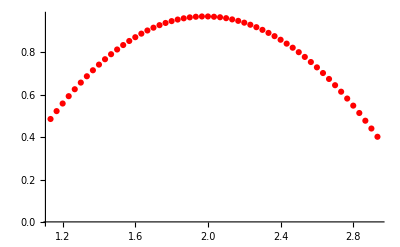

```mathematica
angle79data = {{"ï»¿\"Latest: Time (s)\"","Latest: Position (m)","Latest: Velocity (m/s)","Latest: Acceleration (m/sÂ.b2)"},{0.033333,0.1840195,-0.00371587049204,0.0557386147667},{0.066666,0.183848,-0.00185793524602,0.0521656266406},{0.099999,0.183848,0,0.0394457889118},{0.133332,0.183848,0.00185793524602,-0.00905156991938},{0.166665,0.1840195,0.000857508575086,-0.0949223845493},{0.199998,0.1840195,-0.00357295239619,-0.178173007887},{0.233331,0.184191,-0.0171501715017,-0.0890865039434},{0.266664,0.1823045,-0.0154351543515,0.151256497337},{0.299997,0.1826475,0.000142918095848,0.203303024373},{0.33333,0.182819,0.00385878858789,0.0887292051308},{0.366663,0.1829905,0.00443046097128,-0.00833697229417},{0.399996,0.183162,0.00200085334187,-0.0687204716248},{0.433329,0.183162,-0.00157209905432,-0.0764619458979},{0.466662,0.1829905,-0.00357295239619,-0.0577633080382},{0.499995,0.1829905,-0.0060025600256,-0.0253682156951},{0.533328,0.182476,-0.00643131431314,0.0347770844271},{0.566661,0.1823045,0.000285836191695,0.00559768139751},{0.599994,0.183162,-0.00828924955916,0.0173885422136},{0.633327,0.181104,-0.00228668953356,0.117432209744},{0.66666,0.182819,0.00871800384671,0.00774147427315},{0.699993,0.182819,-0.00743174098408,0.0507364313902},{0.733326,0.1812755,0.00457337906712,0.288697440587},{0.766659,0.1829905,0.0172930895976,0.511413700445},{0.799992,0.182476,0.0311561448948,1.3122394391},{0.833325,0.1860775,0.0543088764221,3.66493302052},{0.866658,0.1829905,0.197941562749,7.67108640707},{0.899991,0.187278,0.653993206599,8.72857179279},{0.933324,0.2289525,0.991279912799,4.58354826773},{0.966657,0.270284,0.944974449744,1.22779781972},{0.99999,0.3009825,0.693295682957,6.86680677989},{1.033323,0.2745715,1.44961824618,10.9389413472},{1.066656,0.406798,1.96626716267,1.26102660929},{1.099989,0.4471005,1.42732302323,-6.22271612037},{1.133322,0.485688,1.21408922423,-5.12545146685},{1.166655,0.5229035,1.09646763134,-3.07074509515},{1.199988,0.558747,1.05516430164,-1.69895585395},{1.233321,0.59339,1.01014510145,-1.42050097932},{1.266654,0.6261465,0.963267966013,-1.37417123329},{1.299987,0.657531,0.917962929629,-1.37143194239},{1.33332,0.687372,0.872086220862,-1.37012184674},{1.366653,0.7156695,0.826352430191,-1.36202307366},{1.399986,0.7424235,0.781476148095,-1.35797368712},{1.433319,0.7678055,0.735885275519,-1.3546388982},{1.466652,0.7914725,0.690580239136,-1.33725035598},{1.499985,0.8137675,0.647133137998,-1.32688869042},{1.533318,0.8346905,0.602256855902,-1.31938541535},{1.566651,0.8538985,0.558095164285,-1.2924689048},{1.599984,0.8717345,0.517506425064,-1.30580806048},{1.633317,0.8885415,0.473201815351,-1.37321843645},{1.66665,0.903462,0.424180908476,-1.39739565611},{1.699983,0.9166675,0.378447117805,-1.3775060222},{1.733316,0.9286725,0.333284999517,-1.37262293843},{1.766649,0.9389625,0.28669370027,-1.35976018118},{1.799982,0.947709,0.242103254366,-1.33594026034},{1.833315,0.9550835,0.198084480845,-1.32438759873},{1.866648,0.9609145,0.15420862542,-1.32379210071},{1.899981,0.9653735,0.110046933803,-1.32772238765},{1.933314,0.968289,0.0650277336107,-1.31069114425},{1.966647,0.969661,0.0217235505688,-1.26948268119},{1.99998,0.969661,-0.0194368610353,-1.23827858489},{2.033313,0.968289,-0.0588822554892,-1.25983561325},{2.066646,0.965888,-0.102186438531,-1.31366863435},{2.099979,0.9616005,-0.148777737777,-1.30950014821},{2.133312,0.9557695,-0.190509821765,-1.27674775705},{2.166645,0.9489095,-0.232384823848,-1.27841515151},{2.199978,0.9403345,-0.275403170698,-1.28972961391},{2.233311,0.930559,-0.318850271836,-1.29020601232},{2.266644,0.9190685,-0.362011536782,-1.27281747011},{2.299977,0.9063775,-0.40374362077,-1.25280873661},{2.33331,0.892143,-0.445189868565,-1.23911228212},{2.366643,0.876708,-0.486350280169,-1.22660682368},{2.399976,0.8597295,-0.527653609869,-1.20397789888},{2.433309,0.841379,-0.565383987173,-1.21779345297},{2.466642,0.822171,-0.606830234969,-1.28282183686},{2.499975,0.8010765,-0.652278189449,-1.31176304069},{2.533308,0.77861,-0.696154044874,-1.28853861787},{2.566641,0.7546,-0.738171965053,-1.2582873184},{2.599974,0.7293895,-0.779475294753,-1.24149427421},{2.633307,0.7026355,-0.820635706357,-1.23589659281},{2.66664,0.674681,-0.861796117961,-1.23422919835},{2.699973,0.645183,-0.902956529565,-1.23101350904},{2.733306,0.6144845,-0.943974023074,-1.2242248316},{2.766639,0.5822425,-0.984848598486,-1.20695538899},{2.799972,0.5488,-1.02443691104,-1.18873314954},{2.833305,0.5139855,-1.06473981406,-1.16455592989},{2.866638,0.4776275,-1.10061225612,-1.18920954796},{2.899971,0.440755,-1.14048640486,-1.31759892129},{2.933304,0.4018245,-1.18893563936,-1.38393740083},{2.966637,0.361522,-1.23667028337,-1.17849058358},{2.99997,0.3198475,-1.29483794838,0.157092377943},{3.033303,0.273714,-1.27711610449,3.2336733537},{3.066636,0.232554,-1.15177693444,8.03505479751},{3.099969,0.1850485,-0.699441161078,11.1951245958},{3.133302,0.1843625,-0.207802911362,8.71451803949},{3.166635,0.183848,-0.0548805488055,4.10464875923},{3.199968,0.183848,-0.0232956496232,1.56937548457},{3.233301,0.1812755,-0.0062883962173,0.8190479781},{3.266634,0.1826475,0.03372867062,0.378974940572},{3.299967,0.1853915,0.0218664686647,-0.0703878660836},{3.3333,0.1829905,0.0315848991823,-0.516058585009},{3.366633,0.1898505,-0.0181505981726,-0.736035553971},{3.399966,0.1812755,-0.0528796954636,-0.0153638489421},{3.433299,0.183162,-0.00557380573806,0.375401952446},{3.466632,0.1829905,-0.00700298669653,0.206280514479},{3.499965,0.182133,0.0060025600256,0.0149827302087},{3.533298,0.1840195,-0.0032871162045,-0.234816779645},{3.566631,0.182476,-0.0235814858149,-0.0790583172696},{3.599964,0.1812755,-0.0143203932039,0.230529193894},{3.633297,0.1812755,0.000857508575086,0.345543681672},{3.66663,0.1819615,0.0128626286263,0.376735868013}};
Data2 = Table[{angle79data[[n,1]],angle79data[[n,2]]},{n,35,89}]
Experiment2 = ListPlot[Data2, PlotStyle->Red]
```

```mathematica
(* define constants and initial conditions *)
(*{1.099989,0.4471005,1.42732302323,-6.22271612037} *)
Manipulate[g = 9.81;
x=0.4471005;
vx=1.42732302323;
ti =1.099989;
tf = 2.933304;
dt = .02;
m=0.467;
theta=7.9Degree;
(*μ0 = 0.0404;*)
(* define an array where we store the results of the simulation *) 
modeldata ={{ti,x}};


(* set up the procedure for step-by-step solution of the equation of motion *)
For[t=ti,t<=tf,
(* calculate the acceleration *)
gx=-m g Sin[theta];
normal=m g Cos[theta];
fx=μ0 normal ((- vx)/Abs[vx]);
ax = (gx+fx)/m;

(* redefine y, vy, in terms of the values from the previous step *)
vx = vx + ax dt;
x = x + vx dt ;
t= t + dt;

(* add the results of the calculation step to the array *)
modeldata = Append[modeldata,{t,x}];

];
(* plot the simulation and compare with the exact result *)
dataplot = ListPlot[modeldata];
Show[{dataplot,Experiment2}],{μ0,0,0.1}]
```

## Model for Angle of 7.9 (Static model)

```mathematica
angle79data = {{"ï»¿\"Latest: Time (s)\"","Latest: Position (m)","Latest: Velocity (m/s)","Latest: Acceleration (m/sÂ.b2)"},{0.033333,0.1840195,-0.00371587049204,0.0557386147667},{0.066666,0.183848,-0.00185793524602,0.0521656266406},{0.099999,0.183848,0,0.0394457889118},{0.133332,0.183848,0.00185793524602,-0.00905156991938},{0.166665,0.1840195,0.000857508575086,-0.0949223845493},{0.199998,0.1840195,-0.00357295239619,-0.178173007887},{0.233331,0.184191,-0.0171501715017,-0.0890865039434},{0.266664,0.1823045,-0.0154351543515,0.151256497337},{0.299997,0.1826475,0.000142918095848,0.203303024373},{0.33333,0.182819,0.00385878858789,0.0887292051308},{0.366663,0.1829905,0.00443046097128,-0.00833697229417},{0.399996,0.183162,0.00200085334187,-0.0687204716248},{0.433329,0.183162,-0.00157209905432,-0.0764619458979},{0.466662,0.1829905,-0.00357295239619,-0.0577633080382},{0.499995,0.1829905,-0.0060025600256,-0.0253682156951},{0.533328,0.182476,-0.00643131431314,0.0347770844271},{0.566661,0.1823045,0.000285836191695,0.00559768139751},{0.599994,0.183162,-0.00828924955916,0.0173885422136},{0.633327,0.181104,-0.00228668953356,0.117432209744},{0.66666,0.182819,0.00871800384671,0.00774147427315},{0.699993,0.182819,-0.00743174098408,0.0507364313902},{0.733326,0.1812755,0.00457337906712,0.288697440587},{0.766659,0.1829905,0.0172930895976,0.511413700445},{0.799992,0.182476,0.0311561448948,1.3122394391},{0.833325,0.1860775,0.0543088764221,3.66493302052},{0.866658,0.1829905,0.197941562749,7.67108640707},{0.899991,0.187278,0.653993206599,8.72857179279},{0.933324,0.2289525,0.991279912799,4.58354826773},{0.966657,0.270284,0.944974449744,1.22779781972},{0.99999,0.3009825,0.693295682957,6.86680677989},{1.033323,0.2745715,1.44961824618,10.9389413472},{1.066656,0.406798,1.96626716267,1.26102660929},{1.099989,0.4471005,1.42732302323,-6.22271612037},{1.133322,0.485688,1.21408922423,-5.12545146685},{1.166655,0.5229035,1.09646763134,-3.07074509515},{1.199988,0.558747,1.05516430164,-1.69895585395},{1.233321,0.59339,1.01014510145,-1.42050097932},{1.266654,0.6261465,0.963267966013,-1.37417123329},{1.299987,0.657531,0.917962929629,-1.37143194239},{1.33332,0.687372,0.872086220862,-1.37012184674},{1.366653,0.7156695,0.826352430191,-1.36202307366},{1.399986,0.7424235,0.781476148095,-1.35797368712},{1.433319,0.7678055,0.735885275519,-1.3546388982},{1.466652,0.7914725,0.690580239136,-1.33725035598},{1.499985,0.8137675,0.647133137998,-1.32688869042},{1.533318,0.8346905,0.602256855902,-1.31938541535},{1.566651,0.8538985,0.558095164285,-1.2924689048},{1.599984,0.8717345,0.517506425064,-1.30580806048},{1.633317,0.8885415,0.473201815351,-1.37321843645},{1.66665,0.903462,0.424180908476,-1.39739565611},{1.699983,0.9166675,0.378447117805,-1.3775060222},{1.733316,0.9286725,0.333284999517,-1.37262293843},{1.766649,0.9389625,0.28669370027,-1.35976018118},{1.799982,0.947709,0.242103254366,-1.33594026034},{1.833315,0.9550835,0.198084480845,-1.32438759873},{1.866648,0.9609145,0.15420862542,-1.32379210071},{1.899981,0.9653735,0.110046933803,-1.32772238765},{1.933314,0.968289,0.0650277336107,-1.31069114425},{1.966647,0.969661,0.0217235505688,-1.26948268119},{1.99998,0.969661,-0.0194368610353,-1.23827858489},{2.033313,0.968289,-0.0588822554892,-1.25983561325},{2.066646,0.965888,-0.102186438531,-1.31366863435},{2.099979,0.9616005,-0.148777737777,-1.30950014821},{2.133312,0.9557695,-0.190509821765,-1.27674775705},{2.166645,0.9489095,-0.232384823848,-1.27841515151},{2.199978,0.9403345,-0.275403170698,-1.28972961391},{2.233311,0.930559,-0.318850271836,-1.29020601232},{2.266644,0.9190685,-0.362011536782,-1.27281747011},{2.299977,0.9063775,-0.40374362077,-1.25280873661},{2.33331,0.892143,-0.445189868565,-1.23911228212},{2.366643,0.876708,-0.486350280169,-1.22660682368},{2.399976,0.8597295,-0.527653609869,-1.20397789888},{2.433309,0.841379,-0.565383987173,-1.21779345297},{2.466642,0.822171,-0.606830234969,-1.28282183686},{2.499975,0.8010765,-0.652278189449,-1.31176304069},{2.533308,0.77861,-0.696154044874,-1.28853861787},{2.566641,0.7546,-0.738171965053,-1.2582873184},{2.599974,0.7293895,-0.779475294753,-1.24149427421},{2.633307,0.7026355,-0.820635706357,-1.23589659281},{2.66664,0.674681,-0.861796117961,-1.23422919835},{2.699973,0.645183,-0.902956529565,-1.23101350904},{2.733306,0.6144845,-0.943974023074,-1.2242248316},{2.766639,0.5822425,-0.984848598486,-1.20695538899},{2.799972,0.5488,-1.02443691104,-1.18873314954},{2.833305,0.5139855,-1.06473981406,-1.16455592989},{2.866638,0.4776275,-1.10061225612,-1.18920954796},{2.899971,0.440755,-1.14048640486,-1.31759892129},{2.933304,0.4018245,-1.18893563936,-1.38393740083},{2.966637,0.361522,-1.23667028337,-1.17849058358},{2.99997,0.3198475,-1.29483794838,0.157092377943},{3.033303,0.273714,-1.27711610449,3.2336733537},{3.066636,0.232554,-1.15177693444,8.03505479751},{3.099969,0.1850485,-0.699441161078,11.1951245958},{3.133302,0.1843625,-0.207802911362,8.71451803949},{3.166635,0.183848,-0.0548805488055,4.10464875923},{3.199968,0.183848,-0.0232956496232,1.56937548457},{3.233301,0.1812755,-0.0062883962173,0.8190479781},{3.266634,0.1826475,0.03372867062,0.378974940572},{3.299967,0.1853915,0.0218664686647,-0.0703878660836},{3.3333,0.1829905,0.0315848991823,-0.516058585009},{3.366633,0.1898505,-0.0181505981726,-0.736035553971},{3.399966,0.1812755,-0.0528796954636,-0.0153638489421},{3.433299,0.183162,-0.00557380573806,0.375401952446},{3.466632,0.1829905,-0.00700298669653,0.206280514479},{3.499965,0.182133,0.0060025600256,0.0149827302087},{3.533298,0.1840195,-0.0032871162045,-0.234816779645},{3.566631,0.182476,-0.0235814858149,-0.0790583172696},{3.599964,0.1812755,-0.0143203932039,0.230529193894},{3.633297,0.1812755,0.000857508575086,0.345543681672},{3.66663,0.1819615,0.0128626286263,0.376735868013}};
Data2 = Table[{angle79data[[n,1]],angle79data[[n,2]]},{n,35,89}]
Experiment2 = ListPlot[Data2, PlotStyle->Red]
```

{{1.13332,0.485688},{1.16666,0.522904},{1.19999,0.558747},{1.23332,0.59339},{1.26665,0.626147},{1.29999,0.657531},{1.33332,0.687372},{1.36665,0.71567},{1.39999,0.742424},{1.43332,0.767806},{1.46665,0.791473},{1.49999,0.813768},{1.53332,0.834691},{1.56665,0.853899},{1.59998,0.871735},{1.63332,0.888542},{1.66665,0.903462},{1.69998,0.916668},{1.73332,0.928673},{1.76665,0.938963},{1.79998,0.947709},{1.83332,0.955084},{1.86665,0.960915},{1.89998,0.965374},{1.93331,0.968289},{1.96665,0.969661},{1.99998,0.969661},{2.03331,0.968289},{2.06665,0.965888},{2.09998,0.961601},{2.13331,0.95577},{2.16665,0.94891},{2.19998,0.940335},{2.23331,0.930559},{2.26664,0.919069},{2.29998,0.906378},{2.33331,0.892143},{2.36664,0.876708},{2.39998,0.85973},{2.43331,0.841379},{2.46664,0.822171},{2.49998,0.801077},{2.53331,0.77861},{2.56664,0.7546},{2.59997,0.72939},{2.63331,0.702636},{2.66664,0.674681},{2.69997,0.645183},{2.73331,0.614485},{2.76664,0.582243},{2.79997,0.5488},{2.83331,0.513986},{2.86664,0.477628},{2.89997,0.440755},{2.9333,0.401825}}

-Graphics-

```mathematica
(* define constants and initial conditions *)
(*{1.099989,0.4471005,1.42732302323,-6.22271612037} *)
Manipulate[g = 9.81;
x=0.4471005;
vx=1.42732302323;
ti =1.099989;
tf = 2.933304;
dt = .02;
m=0.467;
theta=7.9Degree;
(*μ0 = 0.0404;*)
(* define an array where we store the results of the simulation *) 
modeldata ={{ti,x}};


(* set up the procedure for step-by-step solution of the equation of motion *)
For[t=ti,t<=tf,
(* calculate the acceleration *)
gx=-m g Sin[theta];
normal=m g Cos[theta];
fx=μ0 normal Abs[vx]((- vx)/Abs[vx]);
ax = (gx+fx)/m;

(* redefine y, vy, in terms of the values from the previous step *)
vx = vx + ax dt;
x = x + vx dt ;
t= t + dt;

(* add the results of the calculation step to the array *)
modeldata = Append[modeldata,{t,x}];

];
(* plot the simulation and compare with the exact result *)
dataplot = ListPlot[modeldata];
Show[{dataplot,Experiment2}],{μ0,0,0.1}]
```

μ0 = 0.0542

## Model for Angle of 7.9 (Dynamic model)

```mathematica
angle79data = {{"ï»¿\"Latest: Time (s)\"","Latest: Position (m)","Latest: Velocity (m/s)","Latest: Acceleration (m/sÂ.b2)"},{0.033333,0.1840195,-0.00371587049204,0.0557386147667},{0.066666,0.183848,-0.00185793524602,0.0521656266406},{0.099999,0.183848,0,0.0394457889118},{0.133332,0.183848,0.00185793524602,-0.00905156991938},{0.166665,0.1840195,0.000857508575086,-0.0949223845493},{0.199998,0.1840195,-0.00357295239619,-0.178173007887},{0.233331,0.184191,-0.0171501715017,-0.0890865039434},{0.266664,0.1823045,-0.0154351543515,0.151256497337},{0.299997,0.1826475,0.000142918095848,0.203303024373},{0.33333,0.182819,0.00385878858789,0.0887292051308},{0.366663,0.1829905,0.00443046097128,-0.00833697229417},{0.399996,0.183162,0.00200085334187,-0.0687204716248},{0.433329,0.183162,-0.00157209905432,-0.0764619458979},{0.466662,0.1829905,-0.00357295239619,-0.0577633080382},{0.499995,0.1829905,-0.0060025600256,-0.0253682156951},{0.533328,0.182476,-0.00643131431314,0.0347770844271},{0.566661,0.1823045,0.000285836191695,0.00559768139751},{0.599994,0.183162,-0.00828924955916,0.0173885422136},{0.633327,0.181104,-0.00228668953356,0.117432209744},{0.66666,0.182819,0.00871800384671,0.00774147427315},{0.699993,0.182819,-0.00743174098408,0.0507364313902},{0.733326,0.1812755,0.00457337906712,0.288697440587},{0.766659,0.1829905,0.0172930895976,0.511413700445},{0.799992,0.182476,0.0311561448948,1.3122394391},{0.833325,0.1860775,0.0543088764221,3.66493302052},{0.866658,0.1829905,0.197941562749,7.67108640707},{0.899991,0.187278,0.653993206599,8.72857179279},{0.933324,0.2289525,0.991279912799,4.58354826773},{0.966657,0.270284,0.944974449744,1.22779781972},{0.99999,0.3009825,0.693295682957,6.86680677989},{1.033323,0.2745715,1.44961824618,10.9389413472},{1.066656,0.406798,1.96626716267,1.26102660929},{1.099989,0.4471005,1.42732302323,-6.22271612037},{1.133322,0.485688,1.21408922423,-5.12545146685},{1.166655,0.5229035,1.09646763134,-3.07074509515},{1.199988,0.558747,1.05516430164,-1.69895585395},{1.233321,0.59339,1.01014510145,-1.42050097932},{1.266654,0.6261465,0.963267966013,-1.37417123329},{1.299987,0.657531,0.917962929629,-1.37143194239},{1.33332,0.687372,0.872086220862,-1.37012184674},{1.366653,0.7156695,0.826352430191,-1.36202307366},{1.399986,0.7424235,0.781476148095,-1.35797368712},{1.433319,0.7678055,0.735885275519,-1.3546388982},{1.466652,0.7914725,0.690580239136,-1.33725035598},{1.499985,0.8137675,0.647133137998,-1.32688869042},{1.533318,0.8346905,0.602256855902,-1.31938541535},{1.566651,0.8538985,0.558095164285,-1.2924689048},{1.599984,0.8717345,0.517506425064,-1.30580806048},{1.633317,0.8885415,0.473201815351,-1.37321843645},{1.66665,0.903462,0.424180908476,-1.39739565611},{1.699983,0.9166675,0.378447117805,-1.3775060222},{1.733316,0.9286725,0.333284999517,-1.37262293843},{1.766649,0.9389625,0.28669370027,-1.35976018118},{1.799982,0.947709,0.242103254366,-1.33594026034},{1.833315,0.9550835,0.198084480845,-1.32438759873},{1.866648,0.9609145,0.15420862542,-1.32379210071},{1.899981,0.9653735,0.110046933803,-1.32772238765},{1.933314,0.968289,0.0650277336107,-1.31069114425},{1.966647,0.969661,0.0217235505688,-1.26948268119},{1.99998,0.969661,-0.0194368610353,-1.23827858489},{2.033313,0.968289,-0.0588822554892,-1.25983561325},{2.066646,0.965888,-0.102186438531,-1.31366863435},{2.099979,0.9616005,-0.148777737777,-1.30950014821},{2.133312,0.9557695,-0.190509821765,-1.27674775705},{2.166645,0.9489095,-0.232384823848,-1.27841515151},{2.199978,0.9403345,-0.275403170698,-1.28972961391},{2.233311,0.930559,-0.318850271836,-1.29020601232},{2.266644,0.9190685,-0.362011536782,-1.27281747011},{2.299977,0.9063775,-0.40374362077,-1.25280873661},{2.33331,0.892143,-0.445189868565,-1.23911228212},{2.366643,0.876708,-0.486350280169,-1.22660682368},{2.399976,0.8597295,-0.527653609869,-1.20397789888},{2.433309,0.841379,-0.565383987173,-1.21779345297},{2.466642,0.822171,-0.606830234969,-1.28282183686},{2.499975,0.8010765,-0.652278189449,-1.31176304069},{2.533308,0.77861,-0.696154044874,-1.28853861787},{2.566641,0.7546,-0.738171965053,-1.2582873184},{2.599974,0.7293895,-0.779475294753,-1.24149427421},{2.633307,0.7026355,-0.820635706357,-1.23589659281},{2.66664,0.674681,-0.861796117961,-1.23422919835},{2.699973,0.645183,-0.902956529565,-1.23101350904},{2.733306,0.6144845,-0.943974023074,-1.2242248316},{2.766639,0.5822425,-0.984848598486,-1.20695538899},{2.799972,0.5488,-1.02443691104,-1.18873314954},{2.833305,0.5139855,-1.06473981406,-1.16455592989},{2.866638,0.4776275,-1.10061225612,-1.18920954796},{2.899971,0.440755,-1.14048640486,-1.31759892129},{2.933304,0.4018245,-1.18893563936,-1.38393740083},{2.966637,0.361522,-1.23667028337,-1.17849058358},{2.99997,0.3198475,-1.29483794838,0.157092377943},{3.033303,0.273714,-1.27711610449,3.2336733537},{3.066636,0.232554,-1.15177693444,8.03505479751},{3.099969,0.1850485,-0.699441161078,11.1951245958},{3.133302,0.1843625,-0.207802911362,8.71451803949},{3.166635,0.183848,-0.0548805488055,4.10464875923},{3.199968,0.183848,-0.0232956496232,1.56937548457},{3.233301,0.1812755,-0.0062883962173,0.8190479781},{3.266634,0.1826475,0.03372867062,0.378974940572},{3.299967,0.1853915,0.0218664686647,-0.0703878660836},{3.3333,0.1829905,0.0315848991823,-0.516058585009},{3.366633,0.1898505,-0.0181505981726,-0.736035553971},{3.399966,0.1812755,-0.0528796954636,-0.0153638489421},{3.433299,0.183162,-0.00557380573806,0.375401952446},{3.466632,0.1829905,-0.00700298669653,0.206280514479},{3.499965,0.182133,0.0060025600256,0.0149827302087},{3.533298,0.1840195,-0.0032871162045,-0.234816779645},{3.566631,0.182476,-0.0235814858149,-0.0790583172696},{3.599964,0.1812755,-0.0143203932039,0.230529193894},{3.633297,0.1812755,0.000857508575086,0.345543681672},{3.66663,0.1819615,0.0128626286263,0.376735868013}};
Data2 = Table[{angle79data[[n,1]],angle79data[[n,2]]},{n,35,89}]
Experiment2 = ListPlot[Data2, PlotStyle->Red]
```

{{1.13332,0.485688},{1.16666,0.522904},{1.19999,0.558747},{1.23332,0.59339},{1.26665,0.626147},{1.29999,0.657531},{1.33332,0.687372},{1.36665,0.71567},{1.39999,0.742424},{1.43332,0.767806},{1.46665,0.791473},{1.49999,0.813768},{1.53332,0.834691},{1.56665,0.853899},{1.59998,0.871735},{1.63332,0.888542},{1.66665,0.903462},{1.69998,0.916668},{1.73332,0.928673},{1.76665,0.938963},{1.79998,0.947709},{1.83332,0.955084},{1.86665,0.960915},{1.89998,0.965374},{1.93331,0.968289},{1.96665,0.969661},{1.99998,0.969661},{2.03331,0.968289},{2.06665,0.965888},{2.09998,0.961601},{2.13331,0.95577},{2.16665,0.94891},{2.19998,0.940335},{2.23331,0.930559},{2.26664,0.919069},{2.29998,0.906378},{2.33331,0.892143},{2.36664,0.876708},{2.39998,0.85973},{2.43331,0.841379},{2.46664,0.822171},{2.49998,0.801077},{2.53331,0.77861},{2.56664,0.7546},{2.59997,0.72939},{2.63331,0.702636},{2.66664,0.674681},{2.69997,0.645183},{2.73331,0.614485},{2.76664,0.582243},{2.79997,0.5488},{2.83331,0.513986},{2.86664,0.477628},{2.89997,0.440755},{2.9333,0.401825}}

-Graphics-

```mathematica
(* define constants and initial conditions *)
(*{1.099989,0.4471005,1.42732302323,-6.22271612037} *)
Manipulate[g = 9.81;
x=0.4471005;
vx=1.42732302323;
ti =1.099989;
tf = 2.933304;
dt = .02;
m=0.467;
theta=7.9Degree;
(*μ0 = 0.0404;*)
(* define an array where we store the results of the simulation *) 
modeldata ={{ti,x}};


(* set up the procedure for step-by-step solution of the equation of motion *)
For[t=ti,t<=tf,
(* calculate the acceleration *)
gx=-m g Sin[theta];
normal=m g Cos[theta];
fx=μ0 normal Abs[vx^2]((- vx)/Abs[vx]);
ax = (gx+fx)/m;

(* redefine y, vy, in terms of the values from the previous step *)
vx = vx + ax dt;
x = x + vx dt ;
t= t + dt;

(* add the results of the calculation step to the array *)
modeldata = Append[modeldata,{t,x}];

];
(* plot the simulation and compare with the exact result *)
dataplot = ListPlot[modeldata];
Show[{dataplot,Experiment2}],{μ0,0,0.1}]
```

μ0 = 0.051

## Model for Angle of 12.9 (friction model)

```mathematica
angle129data = {{"Latest: Time (s)","Latest: Position (m)","Latest: Velocity (m/s)","Latest: Acceleration (m/sÂ.b2)"},{0.033333,0.1836765,0.0177218438851,0.0148159907628},{0.066666,0.184191,0.0191510248436,-0.0307157879238},{0.099999,0.1850485,0.0183506835068,-0.122482032962},{0.133332,0.185563,0.0118622019554,-0.241129058668},{0.166665,0.1857345,0.00500213335467,-0.402818681333},{0.199998,0.186592,-0.0182935162685,-0.425828724865},{0.233331,0.184534,-0.0391595582622,-0.0307276978842},{0.266664,0.182476,-0.0202943696104,0.357298812607},{0.299997,0.183162,0.00128626286263,0.30156019784},{0.33333,0.1833335,0.00414462477958,0.0880146075056},{0.366663,0.183505,0.00242960762941,-0.027631108175},{0.399996,0.183505,-0.00114334476678,-0.0273929089666},{0.433329,0.1833335,-0.00128626286263,0.048830837723},{0.466662,0.1833335,0.00185793524602,0.133153357498},{0.499995,0.1833335,0.00871800384671,0.171979828468},{0.533328,0.183848,0.01686433531,0.097066177425},{0.566661,0.1847055,0.0181505981726,-0.0849180177963},{0.599994,0.18522,0.0118622019554,-0.295367018422},{0.633327,0.185563,0.000285836191695,-0.492238664169},{0.66666,0.1860775,-0.0297269639363,-0.396363482786},{0.699993,0.183162,-0.0451621182878,0.185438083743},{0.733326,0.181104,-0.00957551242179,0.545595286851},{0.766659,0.1829905,0.0158639086391,0.246417081095},{0.799992,0.183505,0.0062883962173,-0.0615744953726},{0.833325,0.1833335,-0.00228668953356,0.0331096899683},{0.866658,0.1829905,-0.00543088764221,0.750208406871},{0.899991,0.1819615,0.031870735374,2.35698116717},{0.933324,0.1860775,0.0876087927546,5.84707596871},{0.966657,0.181104,0.364726980603,10.2759138506},{0.99999,0.200655,0.89623937906,10.4976773136},{1.033323,0.243187,1.31341730084,3.77581475203},{1.066656,0.3057845,1.20322744894,-3.41017896713},{1.099989,0.33957,0.743888688887,-0.788082081007},{1.133322,0.340599,0.718163431634,12.3837386458},{1.166655,0.3376835,1.93253849205,15.5673901657},{1.199988,0.4964925,2.45876292096,0.156615979526},{1.233321,0.549829,1.70930042634,-10.2588826072},{1.266654,0.590989,1.32227822278,-8.67974095506},{1.299987,0.6295765,1.12862420291,-5.1891697551},{1.33332,0.6655915,1.04773256066,-2.92889746655},{1.366653,0.699377,0.976130594639,-2.31791649699},{1.399986,0.7307615,0.902241939086,-2.22144581758},{1.433319,0.7595735,0.827209938766,-2.20632016785},{1.466652,0.785813,0.75446462798,-2.18023735453},{1.499985,0.809823,0.683005580056,-2.18166654978},{1.533318,0.831432,0.60954567879,-2.19822139476},{1.566651,0.8504685,0.535799941333,-2.20274717972},{1.599984,0.867104,0.462768794355,-2.2078684627},{1.633317,0.8813385,0.389308893089,-2.22382780967},{1.66665,0.893172,0.313276466098,-2.2048909726},{1.699983,0.90209,0.240816991503,-2.14653216654},{1.733316,0.9091215,0.171358796921,-2.11771006232},{1.766649,0.9135805,0.100614339477,-2.11759096272},{1.799982,0.91581,0.0302986363197,-2.12485603857},{1.833315,0.9156385,-0.0411604116041,-2.12747622987},{1.866648,0.913066,-0.112333623336,-2.10746749636},{1.899981,0.9080925,-0.181934736014,-2.08138468304},{1.933314,0.9008895,-0.250249585829,-2.07793079452},{1.966647,0.891457,-0.319707780411,-2.09543843634},{1.99998,0.8796235,-0.390452237856,-2.10103611773},{2.033313,0.865389,-0.460339186725,-2.09007895415},{2.066646,0.848925,-0.529797381307,-2.07650159927},{2.099979,0.83006,-0.598826821602,-2.06268604518},{2.133312,0.8089655,-0.666855835225,-2.0632815432},{2.166645,0.7856415,-0.735885275519,-2.07971728858},{2.199978,0.7599165,-0.805486388197,-2.09639123317},{2.233311,0.731962,-0.875659173258,-2.10734839676},{2.266644,0.7016065,-0.947261139278,-2.08150378265},{2.299977,0.6686785,-1.0152901529,-2.03148194888},{2.33331,0.633864,-1.08146123128,-2.01278331102},{2.366643,0.5966485,-1.14906149061,-2.00849572527},{2.399976,0.5572035,-1.21523256899,-2.01075861775},{2.433309,0.5157005,-1.28311866452,-2.01361700825},{2.466642,0.471625,-1.35000433338,-1.9838421072},{2.499975,0.425663,-1.41603249366,-1.83496760195},{2.533308,0.3773,-1.48391858919,-1.04617092331},{2.566641,0.3267075,-1.52736569032,1.29866208422},{2.599974,0.2738855,-1.47920229202,5.90668532062},{2.633307,0.218834,-1.14891857252,10.610405089},{2.66664,0.190022,-0.635413854139,11.4340979516},{2.699973,0.1833335,-0.279619254526,9.37028046023},{2.733306,0.183505,-0.0888950556172,7.3602364401}};
```

{{1.29999,0.629577},{1.33332,0.665592},{1.36665,0.699377},{1.39999,0.730762},{1.43332,0.759574},{1.46665,0.785813},{1.49999,0.809823},{1.53332,0.831432},{1.56665,0.850469},{1.59998,0.867104},{1.63332,0.881339},{1.66665,0.893172},{1.69998,0.90209},{1.73332,0.909122},{1.76665,0.913581},{1.79998,0.91581},{1.83332,0.915639},{1.86665,0.913066},{1.89998,0.908093},{1.93331,0.90089},{1.96665,0.891457},{1.99998,0.879624},{2.03331,0.865389},{2.06665,0.848925},{2.09998,0.83006},{2.13331,0.808966},{2.16665,0.785642},{2.19998,0.759917},{2.23331,0.731962},{2.26664,0.701607},{2.29998,0.668679},{2.33331,0.633864},{2.36664,0.596649},{2.39998,0.557204},{2.43331,0.515701},{2.46664,0.471625}}

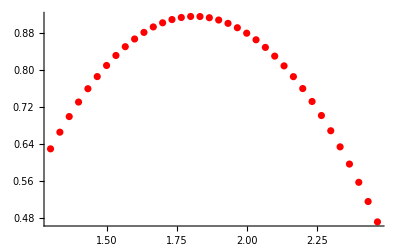

```mathematica
Data3 = Table[{angle129data[[n,1]],angle129data[[n,2]]},{n,40,75}]
Experiment3 = ListPlot[Data3, PlotStyle->Red]
```

```mathematica
{1.299987,0.6295765,1.12862420291,-5.1891697551}
{1.266654,0.590989,1.32227822278,-8.67974095506}
```

{1.29999,0.629577,1.12862,-5.18917}

{1.26665,0.590989,1.32228,-8.67974}

```mathematica
(* define constants and initial conditions *)

Manipulate[g = 9.81;
x=0.590989;
vx=1.32227822278;
ti = 1.266654;
tf = 2.466642;
dt = .02;
m=0.467;
theta=12.9Degree;
(*μ0 = 0.04;*)
(* define an array where we store the results of the simulation *) 
modeldata ={{ti,x}};


(* set up the procedure for step-by-step solution of the equation of motion *)
For[t=ti,t<=tf,
(* calculate the acceleration *)
gx=-m g Sin[theta];
normal=m g Cos[theta];
fx=μ0 normal ((- vx)/Abs[vx]);
ax = (gx+fx)/m;

(* redefine y, vy, in terms of the values from the previous step *)
vx = vx + ax dt;
x = x + vx dt ;
t= t + dt;

(* add the results of the calculation step to the array *)
modeldata = Append[modeldata,{t,x}];

];
(* plot the simulation and compare with the exact result *)
dataplot = ListPlot[modeldata];
Show[{dataplot,Experiment3}],{μ0,0,0.1}]
```

μ0 = 0.0412

## Model for Angle of 12.9 (Static model)

```mathematica
angle129data = {{"Latest: Time (s)","Latest: Position (m)","Latest: Velocity (m/s)","Latest: Acceleration (m/sÂ.b2)"},{0.033333,0.1836765,0.0177218438851,0.0148159907628},{0.066666,0.184191,0.0191510248436,-0.0307157879238},{0.099999,0.1850485,0.0183506835068,-0.122482032962},{0.133332,0.185563,0.0118622019554,-0.241129058668},{0.166665,0.1857345,0.00500213335467,-0.402818681333},{0.199998,0.186592,-0.0182935162685,-0.425828724865},{0.233331,0.184534,-0.0391595582622,-0.0307276978842},{0.266664,0.182476,-0.0202943696104,0.357298812607},{0.299997,0.183162,0.00128626286263,0.30156019784},{0.33333,0.1833335,0.00414462477958,0.0880146075056},{0.366663,0.183505,0.00242960762941,-0.027631108175},{0.399996,0.183505,-0.00114334476678,-0.0273929089666},{0.433329,0.1833335,-0.00128626286263,0.048830837723},{0.466662,0.1833335,0.00185793524602,0.133153357498},{0.499995,0.1833335,0.00871800384671,0.171979828468},{0.533328,0.183848,0.01686433531,0.097066177425},{0.566661,0.1847055,0.0181505981726,-0.0849180177963},{0.599994,0.18522,0.0118622019554,-0.295367018422},{0.633327,0.185563,0.000285836191695,-0.492238664169},{0.66666,0.1860775,-0.0297269639363,-0.396363482786},{0.699993,0.183162,-0.0451621182878,0.185438083743},{0.733326,0.181104,-0.00957551242179,0.545595286851},{0.766659,0.1829905,0.0158639086391,0.246417081095},{0.799992,0.183505,0.0062883962173,-0.0615744953726},{0.833325,0.1833335,-0.00228668953356,0.0331096899683},{0.866658,0.1829905,-0.00543088764221,0.750208406871},{0.899991,0.1819615,0.031870735374,2.35698116717},{0.933324,0.1860775,0.0876087927546,5.84707596871},{0.966657,0.181104,0.364726980603,10.2759138506},{0.99999,0.200655,0.89623937906,10.4976773136},{1.033323,0.243187,1.31341730084,3.77581475203},{1.066656,0.3057845,1.20322744894,-3.41017896713},{1.099989,0.33957,0.743888688887,-0.788082081007},{1.133322,0.340599,0.718163431634,12.3837386458},{1.166655,0.3376835,1.93253849205,15.5673901657},{1.199988,0.4964925,2.45876292096,0.156615979526},{1.233321,0.549829,1.70930042634,-10.2588826072},{1.266654,0.590989,1.32227822278,-8.67974095506},{1.299987,0.6295765,1.12862420291,-5.1891697551},{1.33332,0.6655915,1.04773256066,-2.92889746655},{1.366653,0.699377,0.976130594639,-2.31791649699},{1.399986,0.7307615,0.902241939086,-2.22144581758},{1.433319,0.7595735,0.827209938766,-2.20632016785},{1.466652,0.785813,0.75446462798,-2.18023735453},{1.499985,0.809823,0.683005580056,-2.18166654978},{1.533318,0.831432,0.60954567879,-2.19822139476},{1.566651,0.8504685,0.535799941333,-2.20274717972},{1.599984,0.867104,0.462768794355,-2.2078684627},{1.633317,0.8813385,0.389308893089,-2.22382780967},{1.66665,0.893172,0.313276466098,-2.2048909726},{1.699983,0.90209,0.240816991503,-2.14653216654},{1.733316,0.9091215,0.171358796921,-2.11771006232},{1.766649,0.9135805,0.100614339477,-2.11759096272},{1.799982,0.91581,0.0302986363197,-2.12485603857},{1.833315,0.9156385,-0.0411604116041,-2.12747622987},{1.866648,0.913066,-0.112333623336,-2.10746749636},{1.899981,0.9080925,-0.181934736014,-2.08138468304},{1.933314,0.9008895,-0.250249585829,-2.07793079452},{1.966647,0.891457,-0.319707780411,-2.09543843634},{1.99998,0.8796235,-0.390452237856,-2.10103611773},{2.033313,0.865389,-0.460339186725,-2.09007895415},{2.066646,0.848925,-0.529797381307,-2.07650159927},{2.099979,0.83006,-0.598826821602,-2.06268604518},{2.133312,0.8089655,-0.666855835225,-2.0632815432},{2.166645,0.7856415,-0.735885275519,-2.07971728858},{2.199978,0.7599165,-0.805486388197,-2.09639123317},{2.233311,0.731962,-0.875659173258,-2.10734839676},{2.266644,0.7016065,-0.947261139278,-2.08150378265},{2.299977,0.6686785,-1.0152901529,-2.03148194888},{2.33331,0.633864,-1.08146123128,-2.01278331102},{2.366643,0.5966485,-1.14906149061,-2.00849572527},{2.399976,0.5572035,-1.21523256899,-2.01075861775},{2.433309,0.5157005,-1.28311866452,-2.01361700825},{2.466642,0.471625,-1.35000433338,-1.9838421072},{2.499975,0.425663,-1.41603249366,-1.83496760195},{2.533308,0.3773,-1.48391858919,-1.04617092331},{2.566641,0.3267075,-1.52736569032,1.29866208422},{2.599974,0.2738855,-1.47920229202,5.90668532062},{2.633307,0.218834,-1.14891857252,10.610405089},{2.66664,0.190022,-0.635413854139,11.4340979516},{2.699973,0.1833335,-0.279619254526,9.37028046023},{2.733306,0.183505,-0.0888950556172,7.3602364401}};
```

```mathematica
Data3 = Table[{angle129data[[n,1]],angle129data[[n,2]]},{n,40,75}]
Experiment3 = ListPlot[Data3, PlotStyle->Red]
```

{{1.29999,0.629577},{1.33332,0.665592},{1.36665,0.699377},{1.39999,0.730762},{1.43332,0.759574},{1.46665,0.785813},{1.49999,0.809823},{1.53332,0.831432},{1.56665,0.850469},{1.59998,0.867104},{1.63332,0.881339},{1.66665,0.893172},{1.69998,0.90209},{1.73332,0.909122},{1.76665,0.913581},{1.79998,0.91581},{1.83332,0.915639},{1.86665,0.913066},{1.89998,0.908093},{1.93331,0.90089},{1.96665,0.891457},{1.99998,0.879624},{2.03331,0.865389},{2.06665,0.848925},{2.09998,0.83006},{2.13331,0.808966},{2.16665,0.785642},{2.19998,0.759917},{2.23331,0.731962},{2.26664,0.701607},{2.29998,0.668679},{2.33331,0.633864},{2.36664,0.596649},{2.39998,0.557204},{2.43331,0.515701},{2.46664,0.471625}}

-Graphics-

```mathematica
{1.299987,0.6295765,1.12862420291,-5.1891697551}
{1.266654,0.590989,1.32227822278,-8.67974095506}
```

{1.29999,0.629577,1.12862,-5.18917}

{1.26665,0.590989,1.32228,-8.67974}

```mathematica
(* define constants and initial conditions *)

Manipulate[g = 9.81;
x=0.590989;
vx=1.32227822278;
ti = 1.266654;
tf = 2.466642;
dt = .02;
m=0.467;
theta=12.9Degree;
(*μ0 = 0.04;*)
(* define an array where we store the results of the simulation *) 
modeldata ={{ti,x}};


(* set up the procedure for step-by-step solution of the equation of motion *)
For[t=ti,t<=tf,
(* calculate the acceleration *)
gx=-m g Sin[theta];
normal=m g Cos[theta];
fx=μ0 normal Abs[vx] ((- vx)/Abs[vx]);
ax = (gx+fx)/m;

(* redefine y, vy, in terms of the values from the previous step *)
vx = vx + ax dt;
x = x + vx dt ;
t= t + dt;

(* add the results of the calculation step to the array *)
modeldata = Append[modeldata,{t,x}];

];
(* plot the simulation and compare with the exact result *)
dataplot = ListPlot[modeldata];
Show[{dataplot,Experiment3}],{μ0,0,0.1}]
```

μ0 = 0.039

## Model for Angle of 12.9 (Dynamic model)

```mathematica
angle129data = {{"Latest: Time (s)","Latest: Position (m)","Latest: Velocity (m/s)","Latest: Acceleration (m/sÂ.b2)"},{0.033333,0.1836765,0.0177218438851,0.0148159907628},{0.066666,0.184191,0.0191510248436,-0.0307157879238},{0.099999,0.1850485,0.0183506835068,-0.122482032962},{0.133332,0.185563,0.0118622019554,-0.241129058668},{0.166665,0.1857345,0.00500213335467,-0.402818681333},{0.199998,0.186592,-0.0182935162685,-0.425828724865},{0.233331,0.184534,-0.0391595582622,-0.0307276978842},{0.266664,0.182476,-0.0202943696104,0.357298812607},{0.299997,0.183162,0.00128626286263,0.30156019784},{0.33333,0.1833335,0.00414462477958,0.0880146075056},{0.366663,0.183505,0.00242960762941,-0.027631108175},{0.399996,0.183505,-0.00114334476678,-0.0273929089666},{0.433329,0.1833335,-0.00128626286263,0.048830837723},{0.466662,0.1833335,0.00185793524602,0.133153357498},{0.499995,0.1833335,0.00871800384671,0.171979828468},{0.533328,0.183848,0.01686433531,0.097066177425},{0.566661,0.1847055,0.0181505981726,-0.0849180177963},{0.599994,0.18522,0.0118622019554,-0.295367018422},{0.633327,0.185563,0.000285836191695,-0.492238664169},{0.66666,0.1860775,-0.0297269639363,-0.396363482786},{0.699993,0.183162,-0.0451621182878,0.185438083743},{0.733326,0.181104,-0.00957551242179,0.545595286851},{0.766659,0.1829905,0.0158639086391,0.246417081095},{0.799992,0.183505,0.0062883962173,-0.0615744953726},{0.833325,0.1833335,-0.00228668953356,0.0331096899683},{0.866658,0.1829905,-0.00543088764221,0.750208406871},{0.899991,0.1819615,0.031870735374,2.35698116717},{0.933324,0.1860775,0.0876087927546,5.84707596871},{0.966657,0.181104,0.364726980603,10.2759138506},{0.99999,0.200655,0.89623937906,10.4976773136},{1.033323,0.243187,1.31341730084,3.77581475203},{1.066656,0.3057845,1.20322744894,-3.41017896713},{1.099989,0.33957,0.743888688887,-0.788082081007},{1.133322,0.340599,0.718163431634,12.3837386458},{1.166655,0.3376835,1.93253849205,15.5673901657},{1.199988,0.4964925,2.45876292096,0.156615979526},{1.233321,0.549829,1.70930042634,-10.2588826072},{1.266654,0.590989,1.32227822278,-8.67974095506},{1.299987,0.6295765,1.12862420291,-5.1891697551},{1.33332,0.6655915,1.04773256066,-2.92889746655},{1.366653,0.699377,0.976130594639,-2.31791649699},{1.399986,0.7307615,0.902241939086,-2.22144581758},{1.433319,0.7595735,0.827209938766,-2.20632016785},{1.466652,0.785813,0.75446462798,-2.18023735453},{1.499985,0.809823,0.683005580056,-2.18166654978},{1.533318,0.831432,0.60954567879,-2.19822139476},{1.566651,0.8504685,0.535799941333,-2.20274717972},{1.599984,0.867104,0.462768794355,-2.2078684627},{1.633317,0.8813385,0.389308893089,-2.22382780967},{1.66665,0.893172,0.313276466098,-2.2048909726},{1.699983,0.90209,0.240816991503,-2.14653216654},{1.733316,0.9091215,0.171358796921,-2.11771006232},{1.766649,0.9135805,0.100614339477,-2.11759096272},{1.799982,0.91581,0.0302986363197,-2.12485603857},{1.833315,0.9156385,-0.0411604116041,-2.12747622987},{1.866648,0.913066,-0.112333623336,-2.10746749636},{1.899981,0.9080925,-0.181934736014,-2.08138468304},{1.933314,0.9008895,-0.250249585829,-2.07793079452},{1.966647,0.891457,-0.319707780411,-2.09543843634},{1.99998,0.8796235,-0.390452237856,-2.10103611773},{2.033313,0.865389,-0.460339186725,-2.09007895415},{2.066646,0.848925,-0.529797381307,-2.07650159927},{2.099979,0.83006,-0.598826821602,-2.06268604518},{2.133312,0.8089655,-0.666855835225,-2.0632815432},{2.166645,0.7856415,-0.735885275519,-2.07971728858},{2.199978,0.7599165,-0.805486388197,-2.09639123317},{2.233311,0.731962,-0.875659173258,-2.10734839676},{2.266644,0.7016065,-0.947261139278,-2.08150378265},{2.299977,0.6686785,-1.0152901529,-2.03148194888},{2.33331,0.633864,-1.08146123128,-2.01278331102},{2.366643,0.5966485,-1.14906149061,-2.00849572527},{2.399976,0.5572035,-1.21523256899,-2.01075861775},{2.433309,0.5157005,-1.28311866452,-2.01361700825},{2.466642,0.471625,-1.35000433338,-1.9838421072},{2.499975,0.425663,-1.41603249366,-1.83496760195},{2.533308,0.3773,-1.48391858919,-1.04617092331},{2.566641,0.3267075,-1.52736569032,1.29866208422},{2.599974,0.2738855,-1.47920229202,5.90668532062},{2.633307,0.218834,-1.14891857252,10.610405089},{2.66664,0.190022,-0.635413854139,11.4340979516},{2.699973,0.1833335,-0.279619254526,9.37028046023},{2.733306,0.183505,-0.0888950556172,7.3602364401}};
```

```mathematica
Data3 = Table[{angle129data[[n,1]],angle129data[[n,2]]},{n,40,75}]
Experiment3 = ListPlot[Data3, PlotStyle->Red]
```

{{1.29999,0.629577},{1.33332,0.665592},{1.36665,0.699377},{1.39999,0.730762},{1.43332,0.759574},{1.46665,0.785813},{1.49999,0.809823},{1.53332,0.831432},{1.56665,0.850469},{1.59998,0.867104},{1.63332,0.881339},{1.66665,0.893172},{1.69998,0.90209},{1.73332,0.909122},{1.76665,0.913581},{1.79998,0.91581},{1.83332,0.915639},{1.86665,0.913066},{1.89998,0.908093},{1.93331,0.90089},{1.96665,0.891457},{1.99998,0.879624},{2.03331,0.865389},{2.06665,0.848925},{2.09998,0.83006},{2.13331,0.808966},{2.16665,0.785642},{2.19998,0.759917},{2.23331,0.731962},{2.26664,0.701607},{2.29998,0.668679},{2.33331,0.633864},{2.36664,0.596649},{2.39998,0.557204},{2.43331,0.515701},{2.46664,0.471625}}

-Graphics-

```mathematica
{1.299987,0.6295765,1.12862420291,-5.1891697551}
{1.266654,0.590989,1.32227822278,-8.67974095506}
```

```mathematica
(* define constants and initial conditions *)

Manipulate[g = 9.81;
x=0.590989;
vx=1.32227822278;
ti = 1.266654;
tf = 2.466642;
dt = .02;
m=0.467;
theta=12.9Degree;
(*μ0 = 0.04;*)
(* define an array where we store the results of the simulation *) 
modeldata ={{ti,x}};


(* set up the procedure for step-by-step solution of the equation of motion *)
For[t=ti,t<=tf,
(* calculate the acceleration *)
gx=-m g Sin[theta];
normal=m g Cos[theta];
fx=μ0 normal Abs[vx^2] ((- vx)/Abs[vx]);
ax = (gx+fx)/m;

(* redefine y, vy, in terms of the values from the previous step *)
vx = vx + ax dt;
x = x + vx dt ;
t= t + dt;

(* add the results of the calculation step to the array *)
modeldata = Append[modeldata,{t,x}];

];
(* plot the simulation and compare with the exact result *)
dataplot = ListPlot[modeldata];
Show[{dataplot,Experiment3}],{μ0,0,0.1}]
```

μ0 = 0.039

## End of test models

## Model for Angle of 3.7 (Final model)

```mathematica
angle37Data={{"Latest: Time (s)","Latest: Position (m)","Latest: Velocity (m/s)","Latest: Acceleration (m/sÂ.b2)"},{0.033333,0.1836765,-0.00743174098408,0.0923736530194},{0.066666,0.1833335,-0.00414462477958,0.0800230240636},{0.099999,0.1833335,-0.00120051200512,0.0558815342918},{0.133332,0.1833335,-0.000285836191695,0.0294890620005},{0.166665,0.1833335,0.000142918095848,0.0182460593638},{0.199998,0.1833335,0.00057167238339,0.0156496879922},{0.233331,0.1833335,0.00171501715017,0.000595498021012},{0.266664,0.183505,0.00128626286263,-0.028822104217},{0.299997,0.183505,-0.00128626286263,-0.0287030046128},{0.33333,0.1833335,-0.00171501715017,0.000238199208405},{0.366663,0.1833335,-0.00057167238339,0.0125054584413},{0.399996,0.1833335,0,-0.0048830837723},{0.433329,0.1833335,-0.000571672383391,-0.0270356101539},{0.466662,0.1833335,-0.00128626286263,-0.0510937302028},{0.499995,0.183505,-0.00843216765501,0.0425185587003},{0.533328,0.182133,0.00100042667093,0.160784465673},{0.566661,0.183848,0.00585964192975,0.166977645092},{0.599994,0.182476,0.0111476114761,0.144706019106},{0.633327,0.1840195,0.0264398477318,-0.157449676756},{0.66666,0.1857345,0.00314419810865,-0.478542209685},{0.699993,0.184534,-0.0264398477318,-0.247965375949},{0.733326,0.182476,-0.0190081067477,0.172456226885},{0.766659,0.1829905,-0.00200085334187,0.397435379223},{0.799992,0.183162,-0.00171501715017,1.14657188966},{0.833325,0.182819,0.0280119467861,3.33264512479},{0.866658,0.1823045,0.16106869402,6.90265576076},{0.899991,0.184534,0.539087057537,8.75548830333},{0.933324,0.219177,0.891808918089,6.37540181295},{0.966657,0.252791,1.00085542522,2.64401121329},{0.99999,0.2882915,1.00957342907,0.340863067227},{1.033323,0.320705,0.976988103214,-0.446980814572},{1.066656,0.3527755,0.960266686,-0.465679452431},{1.099989,0.3839885,0.957551242179,-0.680535138412},{1.133322,0.4176025,0.929110541105,-1.19433083094},{1.166655,0.447615,0.858366083661,-1.18980504598},{1.199988,0.4731685,0.829210792108,-0.634800890399},{1.233321,0.501809,0.829639546395,-0.389813004554},{1.266654,0.529249,0.815347736811,-0.479971404936},{1.299987,0.556346,0.795625039584,-0.580610570487},{1.33332,0.5822425,0.774330243302,-0.629203209001},{1.366653,0.6079675,0.753178365117,-0.646472651611},{1.399986,0.632492,0.731026060261,-0.651951233404},{1.433319,0.6566735,0.709588345883,-0.6518321338},{1.466652,0.679826,0.687436041027,-0.648020946465},{1.499985,0.702464,0.666284162842,-0.641708667443},{1.533318,0.7242445,0.645132284656,-0.648020946465},{1.566651,0.7455105,0.6229799798,-0.6518321338},{1.599984,0.7657475,0.601542265423,-0.651951233404},{1.633317,0.7856415,0.579389960566,-0.648973743299},{1.66665,0.804335,0.558238082381,-0.646829950423},{1.699983,0.822857,0.5369432861,-0.664337592241},{1.733316,0.8401785,0.51421930886,-0.689348509123},{1.766649,0.857157,0.490780741141,-0.706737051337},{1.799982,0.872935,0.466341746751,-0.70030567271},{1.833315,0.8881985,0.443331933319,-0.672436365327},{1.866648,0.902433,0.421894218942,-0.654928723509},{1.899981,0.9163245,0.400599422661,-0.663622994616},{1.933314,0.929187,0.377875445421,-0.678034046724},{1.966647,0.941535,0.35486563199,-0.677676747912},{1.99998,0.952854,0.331569982366,-0.648497344882},{2.033313,0.963487,0.312276039427,-0.635039089607},{2.066646,0.973777,0.290409570762,-0.652546731425},{2.099979,0.9828665,0.26811434781,-0.655762420738},{2.133312,0.991613,0.246533715337,-0.654452325092},{2.166645,0.9993305,0.224381410481,-0.648497344882},{2.199978,1.0065335,0.203229532295,-0.641113169421},{2.233311,1.012879,0.18207765411,-0.644805257152},{2.266644,1.01871,0.160068267349,-0.645400755173},{2.299977,1.023512,0.138916389164,-0.644328858735},{2.33331,1.027971,0.117621592883,-0.655166922717},{2.366643,1.031401,0.0951834518345,-0.663384795407},{2.399976,1.0343165,0.0727453107864,-0.655166922717},{2.433309,1.036203,0.0514505145051,-0.644209759131},{2.466642,1.0377465,0.0302986363197,-0.644328858735},{2.499975,1.038261,0.00828924955916,-0.638850276942},{2.533308,1.038261,-0.0127197105304,-0.620747137103},{2.566641,1.0374035,-0.0331569982366,-0.600142905576},{2.599974,1.0360315,-0.0528796954636,-0.578824076424},{2.633307,1.033802,-0.0708873755404,-0.578347678007},{2.66664,1.031401,-0.0908959089591,-0.58978124001},{2.699973,1.0277995,-0.11219070524,-0.554289557958},{2.733306,1.0236835,-0.127482941496,-0.531541533555},{2.766639,1.019396,-0.145347703477,-0.567509614024},{2.799972,1.0140795,-0.165356236896,-0.603239495285},{2.833305,1.00842,-0.186936869369,-0.601333901618},{2.866638,1.00156,-0.206802484692,-0.560363637772},{2.899971,0.9945285,-0.223809738097,-0.531898832368},{2.933304,0.9866395,-0.240674073407,-0.546190784872},{2.966637,0.978579,-0.259968016347,-0.570248904921},{2.99997,0.969318,-0.279690713574,-0.5696534069},{3.033303,0.9598855,-0.298270066034,-0.558934442522},{3.066636,0.949424,-0.316563582302,-0.556433350834},{3.099969,0.938791,-0.335000016667,-0.563460227482},{3.133302,0.927129,-0.354436877702,-0.563460227482},{3.166635,0.915124,-0.372873312066,-0.556433350834},{3.199968,0.9022615,-0.391166828335,-0.559053542126},{3.233301,0.889056,-0.409746180795,-0.570725303338},{3.266634,0.874993,-0.429468878022,-0.57560838711},{3.299967,0.8604155,-0.448905739057,-0.562388331044},{3.3333,0.8449805,-0.466484664847,-0.559291741334},{3.366633,0.829374,-0.485206935403,-0.578585877215},{3.399966,0.8127385,-0.506501731684,-0.563341127877},{3.433299,0.795417,-0.523080230802,-0.54047400387},{3.466632,0.777924,-0.541087910879,-0.552145765082},{3.499965,0.759402,-0.560238935723,-0.556671550042},{3.533298,0.740537,-0.578675370087,-0.551073868644},{3.566631,0.7208145,-0.59682596826,-0.548334577748},{3.599964,0.700749,-0.614976566432,-0.552383964291},{3.633297,0.679826,-0.633413000797,-0.562626530252},{3.66663,0.65856,-0.652849861832,-0.563222028273},{3.699963,0.636265,-0.671286296196,-0.555718753208},{3.733296,0.6137985,-0.689579812465,-0.555718753208},{3.766629,0.590303,-0.708016246829,-0.562626530252},{3.799962,0.566636,-0.727453107864,-0.559291741334},{3.833295,0.5417685,-0.745889542229,-0.537377414161},{3.866628,0.516901,-0.763325549922,-0.520822569177},{3.899961,0.490833,-0.780332803328,-0.518678776301},{3.933294,0.464765,-0.794624612913,-0.59656991745},{3.966627,0.438354,-0.821493214932,-0.637540181295},{3.99996,0.4097135,-0.841358830255,-0.56739051442},{4.033293,0.382102,-0.857222738894,-0.538449310599},{4.066626,0.3527755,-0.877088354217,-0.50105203488},{4.099959,0.323449,-0.892237672377,-0.375759251259},{4.133292,0.293265,-0.906958236249,0.0656238819155},{4.166625,0.263081,-0.910817024837,1.39286987115},{4.199958,0.2316965,-0.862653626536,4.06903797757},{4.233291,0.200312,-0.654564878982,6.89741537817},{4.266624,0.1833335,-0.317421090878,7.14037857075},{4.299957,0.1829905,-0.0843216765501,4.57294840296},{4.33329,0.1833335,-0.0167214172142,1.85438083743},{4.366623,0.183162,-0.0124338743387,0.535471820494},{4.399956,0.1819615,-0.00786049527162,0.212116395084},{4.433289,0.182819,-0.00500213335467,0.256064149035},{4.466622,0.1812755,0.00743174098408,0.366350382527},{4.499955,0.182819,0.0308703087031,0.169597836384},{4.533288,0.184534,0.0230098134315,-0.153876688629},{4.566621,0.1843625,0.0117192838595,-0.247608077137},{4.599954,0.1850485,0.00528796954636,-0.258327041515},{4.633287,0.18522,-0.0108617752844,-0.103021157635},{4.66662,0.183505,-0.00500213335467,0.118623205786},{4.699953,0.184534,0.00814633146331,0.0634800890399},{4.733286,0.184877,0.0027154438211,-0.0697923680626},{4.766619,0.1850485,-0.0092896762301,0.0749136510433},{4.799952,0.1829905,0.00728882288823,0.197943542184},{4.833285,0.1853915,0.0254394210609,-0.200063515139},{4.866618,0.1867635,-0.00814633146331,-0.525276894374},{4.899951,0.184534,-0.0343003430034,-0.210949218963},{4.933284,0.1829905,-0.0234099840998,0.169216717651},{4.966617,0.1829905,-0.00986134861349,0.269010276012},{4.99995,0.1829905,-0.00257252572526,0.26640199468}};
Data1 = Table[{angle37Data[[n,1]],angle37Data[[n,2]]},{n,30,120}]
Experiment1= ListPlot[Data1,PlotStyle->Red]
```

{{0.966657,0.252791},{0.99999,0.288292},{1.03332,0.320705},{1.06666,0.352776},{1.09999,0.383989},{1.13332,0.417603},{1.16666,0.447615},{1.19999,0.473169},{1.23332,0.501809},{1.26665,0.529249},{1.29999,0.556346},{1.33332,0.582243},{1.36665,0.607968},{1.39999,0.632492},{1.43332,0.656674},{1.46665,0.679826},{1.49999,0.702464},{1.53332,0.724245},{1.56665,0.745511},{1.59998,0.765748},{1.63332,0.785642},{1.66665,0.804335},{1.69998,0.822857},{1.73332,0.840179},{1.76665,0.857157},{1.79998,0.872935},{1.83332,0.888199},{1.86665,0.902433},{1.89998,0.916325},{1.93331,0.929187},{1.96665,0.941535},{1.99998,0.952854},{2.03331,0.963487},{2.06665,0.973777},{2.09998,0.982867},{2.13331,0.991613},{2.16665,0.999331},{2.19998,1.00653},{2.23331,1.01288},{2.26664,1.01871},{2.29998,1.02351},{2.33331,1.02797},{2.36664,1.0314},{2.39998,1.03432},{2.43331,1.0362},{2.46664,1.03775},{2.49998,1.03826},{2.53331,1.03826},{2.56664,1.0374},{2.59997,1.03603},{2.63331,1.0338},{2.66664,1.0314},{2.69997,1.0278},{2.73331,1.02368},{2.76664,1.0194},{2.79997,1.01408},{2.83331,1.00842},{2.86664,1.00156},{2.89997,0.994529},{2.9333,0.98664},{2.96664,0.978579},{2.99997,0.969318},{3.0333,0.959886},{3.06664,0.949424},{3.09997,0.938791},{3.1333,0.927129},{3.16664,0.915124},{3.19997,0.902262},{3.2333,0.889056},{3.26663,0.874993},{3.29997,0.860416},{3.3333,0.844981},{3.36663,0.829374},{3.39997,0.812739},{3.4333,0.795417},{3.46663,0.777924},{3.49997,0.759402},{3.5333,0.740537},{3.56663,0.720815},{3.59996,0.700749},{3.6333,0.679826},{3.66663,0.65856},{3.69996,0.636265},{3.7333,0.613799},{3.76663,0.590303},{3.79996,0.566636},{3.8333,0.541769},{3.86663,0.516901},{3.89996,0.490833},{3.93329,0.464765},{3.96663,0.438354}}

-Graphics-

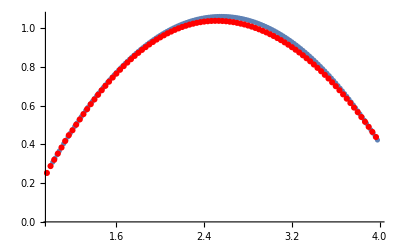

```mathematica
(* define constants and initial conditions *)
(*{0.933324,0.219177,0.891808918089,6.37540181295}, 1 before start
{0.99999,0.2882915,1.00957342907,0.340863067227},1 after start
{1.033323,0.320705,0.976988103214,-0.446980814572}, 2 after start*)
g = 9.81;
x=0.2882915;
vx=1.00957342907;
ti =0.99999;
tf = 3.966627;
dt = .02;
m=0.467;
theta=3.7Degree;
μ0 = 0.0036;
(* define an array where we store the results of the simulation *) 
modeldata ={{ti,x}};


(* set up the procedure for step-by-step solution of the equation of motion *)
For[t=ti,t<=tf,
(* calculate the acceleration *)
gx=-m g Sin[theta];
normal=m g Cos[theta];
fx=μ0 normal Abs[vx^2] ((- vx)/Abs[vx]);
ax = (gx+fx)/m;

(* redefine y, vy, in terms of the values from the previous step *)
vx = vx + ax dt;
x = x + vx dt ;
t= t + dt;

(* add the results of the calculation step to the array *)
modeldata = Append[modeldata,{t,x}];

];
(* plot the simulation and compare with the exact result *)
dataplot = ListPlot[modeldata];
Show[{dataplot,Experiment1}]
```

)

μ0 = 0.0036

## Model for Angle of 7.9 (Final model)

```mathematica
angle79data = {{"ï»¿\"Latest: Time (s)\"","Latest: Position (m)","Latest: Velocity (m/s)","Latest: Acceleration (m/sÂ.b2)"},{0.033333,0.1840195,-0.00371587049204,0.0557386147667},{0.066666,0.183848,-0.00185793524602,0.0521656266406},{0.099999,0.183848,0,0.0394457889118},{0.133332,0.183848,0.00185793524602,-0.00905156991938},{0.166665,0.1840195,0.000857508575086,-0.0949223845493},{0.199998,0.1840195,-0.00357295239619,-0.178173007887},{0.233331,0.184191,-0.0171501715017,-0.0890865039434},{0.266664,0.1823045,-0.0154351543515,0.151256497337},{0.299997,0.1826475,0.000142918095848,0.203303024373},{0.33333,0.182819,0.00385878858789,0.0887292051308},{0.366663,0.1829905,0.00443046097128,-0.00833697229417},{0.399996,0.183162,0.00200085334187,-0.0687204716248},{0.433329,0.183162,-0.00157209905432,-0.0764619458979},{0.466662,0.1829905,-0.00357295239619,-0.0577633080382},{0.499995,0.1829905,-0.0060025600256,-0.0253682156951},{0.533328,0.182476,-0.00643131431314,0.0347770844271},{0.566661,0.1823045,0.000285836191695,0.00559768139751},{0.599994,0.183162,-0.00828924955916,0.0173885422136},{0.633327,0.181104,-0.00228668953356,0.117432209744},{0.66666,0.182819,0.00871800384671,0.00774147427315},{0.699993,0.182819,-0.00743174098408,0.0507364313902},{0.733326,0.1812755,0.00457337906712,0.288697440587},{0.766659,0.1829905,0.0172930895976,0.511413700445},{0.799992,0.182476,0.0311561448948,1.3122394391},{0.833325,0.1860775,0.0543088764221,3.66493302052},{0.866658,0.1829905,0.197941562749,7.67108640707},{0.899991,0.187278,0.653993206599,8.72857179279},{0.933324,0.2289525,0.991279912799,4.58354826773},{0.966657,0.270284,0.944974449744,1.22779781972},{0.99999,0.3009825,0.693295682957,6.86680677989},{1.033323,0.2745715,1.44961824618,10.9389413472},{1.066656,0.406798,1.96626716267,1.26102660929},{1.099989,0.4471005,1.42732302323,-6.22271612037},{1.133322,0.485688,1.21408922423,-5.12545146685},{1.166655,0.5229035,1.09646763134,-3.07074509515},{1.199988,0.558747,1.05516430164,-1.69895585395},{1.233321,0.59339,1.01014510145,-1.42050097932},{1.266654,0.6261465,0.963267966013,-1.37417123329},{1.299987,0.657531,0.917962929629,-1.37143194239},{1.33332,0.687372,0.872086220862,-1.37012184674},{1.366653,0.7156695,0.826352430191,-1.36202307366},{1.399986,0.7424235,0.781476148095,-1.35797368712},{1.433319,0.7678055,0.735885275519,-1.3546388982},{1.466652,0.7914725,0.690580239136,-1.33725035598},{1.499985,0.8137675,0.647133137998,-1.32688869042},{1.533318,0.8346905,0.602256855902,-1.31938541535},{1.566651,0.8538985,0.558095164285,-1.2924689048},{1.599984,0.8717345,0.517506425064,-1.30580806048},{1.633317,0.8885415,0.473201815351,-1.37321843645},{1.66665,0.903462,0.424180908476,-1.39739565611},{1.699983,0.9166675,0.378447117805,-1.3775060222},{1.733316,0.9286725,0.333284999517,-1.37262293843},{1.766649,0.9389625,0.28669370027,-1.35976018118},{1.799982,0.947709,0.242103254366,-1.33594026034},{1.833315,0.9550835,0.198084480845,-1.32438759873},{1.866648,0.9609145,0.15420862542,-1.32379210071},{1.899981,0.9653735,0.110046933803,-1.32772238765},{1.933314,0.968289,0.0650277336107,-1.31069114425},{1.966647,0.969661,0.0217235505688,-1.26948268119},{1.99998,0.969661,-0.0194368610353,-1.23827858489},{2.033313,0.968289,-0.0588822554892,-1.25983561325},{2.066646,0.965888,-0.102186438531,-1.31366863435},{2.099979,0.9616005,-0.148777737777,-1.30950014821},{2.133312,0.9557695,-0.190509821765,-1.27674775705},{2.166645,0.9489095,-0.232384823848,-1.27841515151},{2.199978,0.9403345,-0.275403170698,-1.28972961391},{2.233311,0.930559,-0.318850271836,-1.29020601232},{2.266644,0.9190685,-0.362011536782,-1.27281747011},{2.299977,0.9063775,-0.40374362077,-1.25280873661},{2.33331,0.892143,-0.445189868565,-1.23911228212},{2.366643,0.876708,-0.486350280169,-1.22660682368},{2.399976,0.8597295,-0.527653609869,-1.20397789888},{2.433309,0.841379,-0.565383987173,-1.21779345297},{2.466642,0.822171,-0.606830234969,-1.28282183686},{2.499975,0.8010765,-0.652278189449,-1.31176304069},{2.533308,0.77861,-0.696154044874,-1.28853861787},{2.566641,0.7546,-0.738171965053,-1.2582873184},{2.599974,0.7293895,-0.779475294753,-1.24149427421},{2.633307,0.7026355,-0.820635706357,-1.23589659281},{2.66664,0.674681,-0.861796117961,-1.23422919835},{2.699973,0.645183,-0.902956529565,-1.23101350904},{2.733306,0.6144845,-0.943974023074,-1.2242248316},{2.766639,0.5822425,-0.984848598486,-1.20695538899},{2.799972,0.5488,-1.02443691104,-1.18873314954},{2.833305,0.5139855,-1.06473981406,-1.16455592989},{2.866638,0.4776275,-1.10061225612,-1.18920954796},{2.899971,0.440755,-1.14048640486,-1.31759892129},{2.933304,0.4018245,-1.18893563936,-1.38393740083},{2.966637,0.361522,-1.23667028337,-1.17849058358},{2.99997,0.3198475,-1.29483794838,0.157092377943},{3.033303,0.273714,-1.27711610449,3.2336733537},{3.066636,0.232554,-1.15177693444,8.03505479751},{3.099969,0.1850485,-0.699441161078,11.1951245958},{3.133302,0.1843625,-0.207802911362,8.71451803949},{3.166635,0.183848,-0.0548805488055,4.10464875923},{3.199968,0.183848,-0.0232956496232,1.56937548457},{3.233301,0.1812755,-0.0062883962173,0.8190479781},{3.266634,0.1826475,0.03372867062,0.378974940572},{3.299967,0.1853915,0.0218664686647,-0.0703878660836},{3.3333,0.1829905,0.0315848991823,-0.516058585009},{3.366633,0.1898505,-0.0181505981726,-0.736035553971},{3.399966,0.1812755,-0.0528796954636,-0.0153638489421},{3.433299,0.183162,-0.00557380573806,0.375401952446},{3.466632,0.1829905,-0.00700298669653,0.206280514479},{3.499965,0.182133,0.0060025600256,0.0149827302087},{3.533298,0.1840195,-0.0032871162045,-0.234816779645},{3.566631,0.182476,-0.0235814858149,-0.0790583172696},{3.599964,0.1812755,-0.0143203932039,0.230529193894},{3.633297,0.1812755,0.000857508575086,0.345543681672},{3.66663,0.1819615,0.0128626286263,0.376735868013}};
Data2 = Table[{angle79data[[n,1]],angle79data[[n,2]]},{n,35,89}]
Experiment2 = ListPlot[Data2, PlotStyle->Red]
```

{{1.13332,0.485688},{1.16666,0.522904},{1.19999,0.558747},{1.23332,0.59339},{1.26665,0.626147},{1.29999,0.657531},{1.33332,0.687372},{1.36665,0.71567},{1.39999,0.742424},{1.43332,0.767806},{1.46665,0.791473},{1.49999,0.813768},{1.53332,0.834691},{1.56665,0.853899},{1.59998,0.871735},{1.63332,0.888542},{1.66665,0.903462},{1.69998,0.916668},{1.73332,0.928673},{1.76665,0.938963},{1.79998,0.947709},{1.83332,0.955084},{1.86665,0.960915},{1.89998,0.965374},{1.93331,0.968289},{1.96665,0.969661},{1.99998,0.969661},{2.03331,0.968289},{2.06665,0.965888},{2.09998,0.961601},{2.13331,0.95577},{2.16665,0.94891},{2.19998,0.940335},{2.23331,0.930559},{2.26664,0.919069},{2.29998,0.906378},{2.33331,0.892143},{2.36664,0.876708},{2.39998,0.85973},{2.43331,0.841379},{2.46664,0.822171},{2.49998,0.801077},{2.53331,0.77861},{2.56664,0.7546},{2.59997,0.72939},{2.63331,0.702636},{2.66664,0.674681},{2.69997,0.645183},{2.73331,0.614485},{2.76664,0.582243},{2.79997,0.5488},{2.83331,0.513986},{2.86664,0.477628},{2.89997,0.440755},{2.9333,0.401825}}

-Graphics-

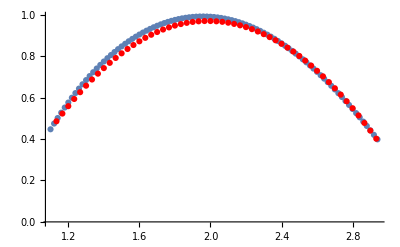

```mathematica
(* define constants and initial conditions *)
(*{1.099989,0.4471005,1.42732302323,-6.22271612037} *)
g = 9.81;
x=0.4471005;
vx=1.42732302323;
ti =1.099989;
tf = 2.933304;
dt = .02;
m=0.467;
theta=7.9Degree;
μ0 = 0.051;
(* define an array where we store the results of the simulation *) 
modeldata ={{ti,x}};


(* set up the procedure for step-by-step solution of the equation of motion *)
For[t=ti,t<=tf,
(* calculate the acceleration *)
gx=-m g Sin[theta];
normal=m g Cos[theta];
fx=μ0 normal Abs[vx^2]((- vx)/Abs[vx]);
ax = (gx+fx)/m;

(* redefine y, vy, in terms of the values from the previous step *)
vx = vx + ax dt;
x = x + vx dt ;
t= t + dt;

(* add the results of the calculation step to the array *)
modeldata = Append[modeldata,{t,x}];

];
(* plot the simulation and compare with the exact result *)
dataplot = ListPlot[modeldata];
Show[{dataplot,Experiment2}]
```

when μ0 = 0.051

## Model for Angle of 12.9 (Final model)

```mathematica
angle129data = {{"Latest: Time (s)","Latest: Position (m)","Latest: Velocity (m/s)","Latest: Acceleration (m/sÂ.b2)"},{0.033333,0.1836765,0.0177218438851,0.0148159907628},{0.066666,0.184191,0.0191510248436,-0.0307157879238},{0.099999,0.1850485,0.0183506835068,-0.122482032962},{0.133332,0.185563,0.0118622019554,-0.241129058668},{0.166665,0.1857345,0.00500213335467,-0.402818681333},{0.199998,0.186592,-0.0182935162685,-0.425828724865},{0.233331,0.184534,-0.0391595582622,-0.0307276978842},{0.266664,0.182476,-0.0202943696104,0.357298812607},{0.299997,0.183162,0.00128626286263,0.30156019784},{0.33333,0.1833335,0.00414462477958,0.0880146075056},{0.366663,0.183505,0.00242960762941,-0.027631108175},{0.399996,0.183505,-0.00114334476678,-0.0273929089666},{0.433329,0.1833335,-0.00128626286263,0.048830837723},{0.466662,0.1833335,0.00185793524602,0.133153357498},{0.499995,0.1833335,0.00871800384671,0.171979828468},{0.533328,0.183848,0.01686433531,0.097066177425},{0.566661,0.1847055,0.0181505981726,-0.0849180177963},{0.599994,0.18522,0.0118622019554,-0.295367018422},{0.633327,0.185563,0.000285836191695,-0.492238664169},{0.66666,0.1860775,-0.0297269639363,-0.396363482786},{0.699993,0.183162,-0.0451621182878,0.185438083743},{0.733326,0.181104,-0.00957551242179,0.545595286851},{0.766659,0.1829905,0.0158639086391,0.246417081095},{0.799992,0.183505,0.0062883962173,-0.0615744953726},{0.833325,0.1833335,-0.00228668953356,0.0331096899683},{0.866658,0.1829905,-0.00543088764221,0.750208406871},{0.899991,0.1819615,0.031870735374,2.35698116717},{0.933324,0.1860775,0.0876087927546,5.84707596871},{0.966657,0.181104,0.364726980603,10.2759138506},{0.99999,0.200655,0.89623937906,10.4976773136},{1.033323,0.243187,1.31341730084,3.77581475203},{1.066656,0.3057845,1.20322744894,-3.41017896713},{1.099989,0.33957,0.743888688887,-0.788082081007},{1.133322,0.340599,0.718163431634,12.3837386458},{1.166655,0.3376835,1.93253849205,15.5673901657},{1.199988,0.4964925,2.45876292096,0.156615979526},{1.233321,0.549829,1.70930042634,-10.2588826072},{1.266654,0.590989,1.32227822278,-8.67974095506},{1.299987,0.6295765,1.12862420291,-5.1891697551},{1.33332,0.6655915,1.04773256066,-2.92889746655},{1.366653,0.699377,0.976130594639,-2.31791649699},{1.399986,0.7307615,0.902241939086,-2.22144581758},{1.433319,0.7595735,0.827209938766,-2.20632016785},{1.466652,0.785813,0.75446462798,-2.18023735453},{1.499985,0.809823,0.683005580056,-2.18166654978},{1.533318,0.831432,0.60954567879,-2.19822139476},{1.566651,0.8504685,0.535799941333,-2.20274717972},{1.599984,0.867104,0.462768794355,-2.2078684627},{1.633317,0.8813385,0.389308893089,-2.22382780967},{1.66665,0.893172,0.313276466098,-2.2048909726},{1.699983,0.90209,0.240816991503,-2.14653216654},{1.733316,0.9091215,0.171358796921,-2.11771006232},{1.766649,0.9135805,0.100614339477,-2.11759096272},{1.799982,0.91581,0.0302986363197,-2.12485603857},{1.833315,0.9156385,-0.0411604116041,-2.12747622987},{1.866648,0.913066,-0.112333623336,-2.10746749636},{1.899981,0.9080925,-0.181934736014,-2.08138468304},{1.933314,0.9008895,-0.250249585829,-2.07793079452},{1.966647,0.891457,-0.319707780411,-2.09543843634},{1.99998,0.8796235,-0.390452237856,-2.10103611773},{2.033313,0.865389,-0.460339186725,-2.09007895415},{2.066646,0.848925,-0.529797381307,-2.07650159927},{2.099979,0.83006,-0.598826821602,-2.06268604518},{2.133312,0.8089655,-0.666855835225,-2.0632815432},{2.166645,0.7856415,-0.735885275519,-2.07971728858},{2.199978,0.7599165,-0.805486388197,-2.09639123317},{2.233311,0.731962,-0.875659173258,-2.10734839676},{2.266644,0.7016065,-0.947261139278,-2.08150378265},{2.299977,0.6686785,-1.0152901529,-2.03148194888},{2.33331,0.633864,-1.08146123128,-2.01278331102},{2.366643,0.5966485,-1.14906149061,-2.00849572527},{2.399976,0.5572035,-1.21523256899,-2.01075861775},{2.433309,0.5157005,-1.28311866452,-2.01361700825},{2.466642,0.471625,-1.35000433338,-1.9838421072},{2.499975,0.425663,-1.41603249366,-1.83496760195},{2.533308,0.3773,-1.48391858919,-1.04617092331},{2.566641,0.3267075,-1.52736569032,1.29866208422},{2.599974,0.2738855,-1.47920229202,5.90668532062},{2.633307,0.218834,-1.14891857252,10.610405089},{2.66664,0.190022,-0.635413854139,11.4340979516},{2.699973,0.1833335,-0.279619254526,9.37028046023},{2.733306,0.183505,-0.0888950556172,7.3602364401}};
```

```mathematica
Data3 = Table[{angle129data[[n,1]],angle129data[[n,2]]},{n,40,75}]
Experiment3 = ListPlot[Data3, PlotStyle->Red]
```

{{1.29999,0.629577},{1.33332,0.665592},{1.36665,0.699377},{1.39999,0.730762},{1.43332,0.759574},{1.46665,0.785813},{1.49999,0.809823},{1.53332,0.831432},{1.56665,0.850469},{1.59998,0.867104},{1.63332,0.881339},{1.66665,0.893172},{1.69998,0.90209},{1.73332,0.909122},{1.76665,0.913581},{1.79998,0.91581},{1.83332,0.915639},{1.86665,0.913066},{1.89998,0.908093},{1.93331,0.90089},{1.96665,0.891457},{1.99998,0.879624},{2.03331,0.865389},{2.06665,0.848925},{2.09998,0.83006},{2.13331,0.808966},{2.16665,0.785642},{2.19998,0.759917},{2.23331,0.731962},{2.26664,0.701607},{2.29998,0.668679},{2.33331,0.633864},{2.36664,0.596649},{2.39998,0.557204},{2.43331,0.515701},{2.46664,0.471625}}

-Graphics-

```mathematica
{1.299987,0.6295765,1.12862420291,-5.1891697551}
{1.266654,0.590989,1.32227822278,-8.67974095506}
```

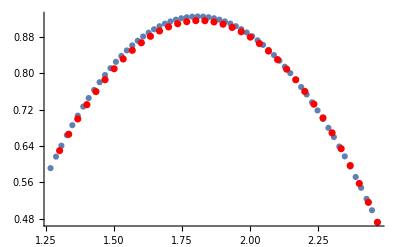

```mathematica
(* define constants and initial conditions *)

g = 9.81;
x=0.590989;
vx=1.32227822278;
ti = 1.266654;
tf = 2.466642;
dt = .02;
m=0.467;
theta=12.9Degree;
μ0 = 0.039;
(* define an array where we store the results of the simulation *) 
modeldata ={{ti,x}};


(* set up the procedure for step-by-step solution of the equation of motion *)
For[t=ti,t<=tf,
(* calculate the acceleration *)
gx=-m g Sin[theta];
normal=m g Cos[theta];
fx=μ0 normal Abs[vx^2] ((- vx)/Abs[vx]);
ax = (gx+fx)/m;

(* redefine y, vy, in terms of the values from the previous step *)
vx = vx + ax dt;
x = x + vx dt ;
t= t + dt;

(* add the results of the calculation step to the array *)
modeldata = Append[modeldata,{t,x}];

];
(* plot the simulation and compare with the exact result *)
dataplot = ListPlot[modeldata];
Show[{dataplot,Experiment3}]
```

when μ0 = 0.039

## Analysis

In order to find the most accurate representation to model friction force, we used three different friction forces to compare and contrast how our model represents collected data.  

Friction:
the friction model would be the worst representation of a friction force due to it’s incapability to match up with our data points.  The μ0 constant used in the model of the 7.9 degree system could not match up with the data, thus giving us an outlier when trying to gather information on which corresponding μ0 value that would work best for all three models.   When comparing the μ0 values from each system, the μ0  values for the friction model were quite different when compared to the μ0 values for the static and dynamic models.  Because our models did not match up to the data for the three varying angles, the friction model not be the best representation for our data.  If our data represented a system that was sliding and had no wheels, this would be a much better representation for our data.  


Static: 
The static model represents how our friction force is linearly dependent on the velocity of the cart.  Because velocity and friction are linearly proportional to one another, this model would best represent a cart moving in a straight path or down a hill.  The inconsistency in our model when compared to the data may have been due to the carts motion from it moving up the ramp to a halt, and the slowing accelerating back down the ramp until it was stopped by the experimentalist.  

Dynamic: 
When comparing the three dymamic models from each angle, it seems as if the friction force represented in this model best represents our data.  The friction force used in this model is dependent on on the velocity squared.  I think this model matches the data best because of the quadratic properties of this friction force and the parabolic motion of the cart.  When only taking into account the static and dynamic models, values for μ0 were similar in value. Being that the values are similar, what determines the better model is how well the model fits the data.  When comparing all data sets and models for varying angles, the dynamic model seems to best represent the data for each angle.

## Conclusions

This lab, like the first lab, clearly shows that there are many things to take into consideration when modeling physical simulations, and that the difficulty in modeling lies mainly in deciding which set of equations best describes the system.  It is likely that the dynamic models are most effective because of their quadratic nature, allowing the model to be more fine-tuned than our statc and friction models.  The friction model likely failed because it only accounted for the frictional force on the object if it were stationary, much like the static model.  Without considering the effect of changing velocities as the cart moves up and down the ramp, our simulations will not be accurate.  We can further be comfortable with our choice of the dynamic model because of how similar the values for μ0 are, considering that we have a small range of values for the angle of the ramp.